```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

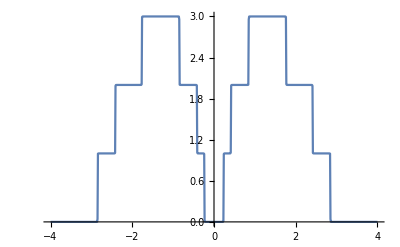

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
ξ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k614[ω_,ϵ1_]:=k614[ω,ϵ1]=Append[{},Table[ξ14[ω,0.001,1,0,ϵ1],{i,100}]];
k613[ω_,ϵ1_]:=k613[ω,ϵ1]=Append[{},Table[ξ13[ω,0.001,1,0,ϵ1],{i,100}]];
k612[ω_,ϵ1_]:=k612[ω,ϵ1]=Append[{},Table[ξ12[ω,0.001,1,0,ϵ1],{i,100}]];
k611[ω_,ϵ1_]:=k611[ω,ϵ1]=Append[{},Table[ξ11[ω,0.001,1,0,ϵ1],{i,100}]];
k610[ω_,ϵ1_]:=k610[ω,ϵ1]=Append[{},Table[ξ10[ω,0.001,1,0,ϵ1],{i,100}]];
k69[ω_,ϵ1_]:=k69[ω,ϵ1]=Append[{},Table[ξ9[ω,0.001,1,0,ϵ1],{i,100}]];
k68[ω_,ϵ1_]:=k68[ω,ϵ1]=Append[{},Table[ξ8[ω,0.001,1,0,ϵ1],{i,100}]];
k67[ω_,ϵ1_]:=k67[ω,ϵ1]=Append[{},Table[ξ7[ω,0.001,1,0,ϵ1],{i,100}]];
k66[ω_,ϵ1_]:=k66[ω,ϵ1]=Append[{},Table[ξ6[ω,0.001,1,0,ϵ1],{i,100}]];
k65[ω_,ϵ1_]:=k65[ω,ϵ1]=Append[{},Table[ξ5[ω,0.001,1,0,ϵ1],{i,100}]];
k64[ω_,ϵ1_]:=k64[ω,ϵ1]=Append[{},Table[ξ4[ω,0.001,1,0,ϵ1],{i,100}]];
k63[ω_,ϵ1_]:=k63[ω,ϵ1]=Append[{},Table[ξ3[ω,0.001,1,0,ϵ1],{i,100}]];
k62[ω_,ϵ1_]:=k62[ω,ϵ1]=Append[{},Table[ξ2[ω,0.001,1,0,ϵ1],{i,100}]];
k61[ω_,ϵ1_]:=k61[ω,ϵ1]=Append[{},Table[ξ1[ω,0.001,1,0,ϵ1],{i,100}]]
```

```mathematica
ρ6[ω_,ϵ1_]:=Join[Mean[k61[ω,ϵ1]],Mean[k62[ω,ϵ1]],Mean[k63[ω,ϵ1]],Mean[k64[ω,ϵ1]],Mean[k65[ω,ϵ1]],Mean[k66[ω,ϵ1]],Mean[k67[ω,ϵ1]],Mean[k68[ω,ϵ1]],Mean[k69[ω,ϵ1]],Mean[k610[ω,ϵ1]],Mean[k611[ω,ϵ1]],Mean[k613[ω,ϵ1]],Mean[k614[ω,ϵ1]]]
```

```mathematica
Mean[ρ6[0.5,0.5]]
```

1.59761

```mathematica
Export["6imp3.csv",Table[{ω,Mean[ρ6[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

6imp3.csv

```mathematica
Export["6imp4.csv",Table[{ω,Mean[ρ6[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

6imp4.csv

```mathematica
Export["6imp6.csv",Table[{ω,Mean[ρ6[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

6imp6.csv

```mathematica
Export["6imp7.csv",Table[{ω,Mean[ρ6[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

6imp7.csv

```mathematica
Export["6imp8.csv",Table[{ω,Mean[ρ6[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

6imp8.csv

```mathematica
Export["6imp9.csv",Table[{ω,Mean[ρ6[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

6imp9.csv

```mathematica
Export["6imp1.csv",Table[{ω,Mean[ρ6[ω,1]]},{ω,Range[0,4,0.01]}]]
```

6imp1.csv

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],k=RandomInteger[{1,7}]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ1]]];
```

```mathematica
ξ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8
]
```

```mathematica
-Im[Mean[Table[ξ1[2,0.001,1,0,0],2000]][[1,1]]]
```

0.409626

```mathematica
Pert[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[SL[ω,δ,t,ϵ]].(ξ1[ω,δ,t,ϵ,ϵ1]-SL[ω,δ,t,ϵ]).ξ1[ω,δ,t,ϵ,ϵ1]
```

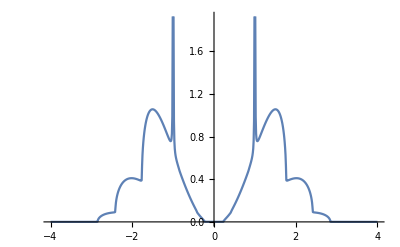

```mathematica
ListLinePlot[Table[{ω,-Im[Mean[Table[ξ1[ω,0.001,1,0,0],1000]][[1,1]]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Table[RandomChoice[{1,2}],100]
```

{2,2,2,1,1,2,1,2,1,2,1,2,1,1,1,2,1,1,1,1,2,2,2,2,2,1,1,1,1,1,1,1,1,1,2,1,1,2,2,1,1,2,2,2,1,1,1,1,2,1,1,2,1,1,1,1,1,2,1,1,1,1,2,1,1,2,2,2,1,2,1,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,1,2,2,1,1,2,2,2,2,2}

```mathematica
Clear[imp4,imp5,imp6,imp7,imp8]
```

```mathematica
Table[{RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},10]
```

{{imp5,imp5,imp1,imp2,imp3,imp3,imp5,imp6},{imp6,imp7,imp3,imp5,imp5,imp4,imp7,imp2},{imp2,imp4,imp2,imp5,imp5,imp4,imp7,imp2},{imp7,imp3,imp8,imp6,imp2,imp7,imp8,imp2},{imp2,imp8,imp6,imp5,imp6,imp6,imp3,imp1},{imp8,imp4,imp1,imp5,imp4,imp4,imp1,imp6},{imp5,imp5,imp1,imp7,imp8,imp3,imp1,imp4},{imp6,imp6,imp6,imp3,imp8,imp5,imp1,imp8},{imp2,imp7,imp8,imp8,imp6,imp8,imp2,imp1},{imp2,imp3,imp3,imp6,imp4,imp7,imp1,imp5}}

```mathematica
RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}],
```

```mathematica
RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8},{100,8}]
```

{{imp4,imp4,imp1,imp4,imp8,imp4,imp5,imp8},{imp8,imp2,imp4,imp1,imp7,imp7,imp3,imp5},{imp8,imp8,imp6,imp6,imp4,imp1,imp6,imp5},{imp6,imp2,imp5,imp6,imp8,imp1,imp8,imp3},{imp4,imp5,imp1,imp1,imp7,imp6,imp2,imp7},{imp4,imp8,imp1,imp8,imp1,imp1,imp1,imp1},{imp1,imp8,imp1,imp3,imp6,imp8,imp4,imp2},{imp3,imp1,imp4,imp8,imp7,imp8,imp5,imp6},{imp4,imp3,imp5,imp4,imp7,imp7,imp1,imp1},{imp6,imp2,imp5,imp6,imp6,imp7,imp1,imp3},{imp4,imp5,imp8,imp2,imp5,imp7,imp5,imp6},{imp7,imp5,imp2,imp4,imp8,imp3,imp3,imp4},{imp7,imp2,imp1,imp2,imp6,imp1,imp5,imp7},{imp5,imp3,imp6,imp4,imp5,imp6,imp4,imp8},{imp6,imp2,imp1,imp4,imp1,imp2,imp5,imp3},{imp8,imp5,imp8,imp3,imp2,imp5,imp7,imp1},{imp7,imp3,imp4,imp2,imp6,imp2,imp7,imp3},{imp5,imp3,imp8,imp3,imp5,imp5,imp8,imp6},{imp7,imp2,imp8,imp2,imp3,imp3,imp4,imp6},{imp2,imp1,imp3,imp4,imp8,imp1,imp3,imp3},{imp7,imp3,imp5,imp1,imp5,imp3,imp3,imp8},{imp4,imp8,imp7,imp3,imp1,imp6,imp3,imp3},{imp8,imp5,imp8,imp3,imp5,imp3,imp7,imp4},{imp1,imp5,imp2,imp6,imp3,imp4,imp5,imp1},{imp1,imp5,imp1,imp5,imp5,imp3,imp7,imp6},{imp7,imp8,imp8,imp5,imp1,imp6,imp3,imp4},{imp1,imp8,imp3,imp1,imp7,imp2,imp3,imp5},{imp5,imp1,imp6,imp8,imp5,imp4,imp2,imp5},{imp4,imp2,imp3,imp4,imp1,imp4,imp4,imp4},{imp2,imp5,imp7,imp5,imp6,imp8,imp7,imp2},{imp1,imp7,imp5,imp1,imp6,imp1,imp8,imp8},{imp5,imp5,imp7,imp3,imp8,imp2,imp1,imp6},{imp4,imp7,imp4,imp5,imp4,imp5,imp4,imp7},{imp5,imp4,imp8,imp6,imp4,imp1,imp3,imp8},{imp2,imp1,imp1,imp2,imp8,imp7,imp6,imp4},{imp1,imp8,imp4,imp8,imp1,imp2,imp2,imp1},{imp8,imp4,imp3,imp4,imp7,imp2,imp3,imp2},{imp5,imp8,imp7,imp5,imp2,imp5,imp1,imp2},{imp7,imp4,imp5,imp6,imp8,imp8,imp2,imp8},{imp3,imp4,imp2,imp5,imp1,imp4,imp3,imp2},{imp5,imp1,imp2,imp6,imp7,imp4,imp2,imp6},{imp7,imp7,imp5,imp3,imp3,imp8,imp5,imp2},{imp8,imp4,imp3,imp2,imp3,imp7,imp1,imp6},{imp6,imp1,imp6,imp3,imp4,imp6,imp6,imp2},{imp2,imp5,imp7,imp7,imp7,imp8,imp1,imp7},{imp6,imp8,imp1,imp5,imp6,imp5,imp6,imp7},{imp7,imp8,imp1,imp5,imp6,imp6,imp5,imp1},{imp3,imp6,imp1,imp2,imp5,imp4,imp7,imp8},{imp4,imp2,imp4,imp3,imp4,imp5,imp6,imp5},{imp5,imp6,imp3,imp7,imp7,imp5,imp6,imp6},{imp8,imp6,imp2,imp3,imp2,imp8,imp8,imp7},{imp1,imp5,imp1,imp6,imp2,imp5,imp2,imp7},{imp8,imp3,imp8,imp8,imp8,imp1,imp6,imp4},{imp2,imp2,imp7,imp8,imp1,imp7,imp1,imp4},{imp7,imp8,imp3,imp5,imp6,imp2,imp3,imp3},{imp4,imp7,imp8,imp6,imp4,imp2,imp1,imp5},{imp8,imp7,imp8,imp3,imp3,imp2,imp8,imp1},{imp2,imp6,imp3,imp1,imp7,imp6,imp3,imp3},{imp8,imp4,imp7,imp2,imp4,imp5,imp4,imp3},{imp6,imp4,imp1,imp6,imp4,imp4,imp8,imp5},{imp7,imp7,imp2,imp5,imp6,imp8,imp4,imp8},{imp4,imp7,imp4,imp5,imp2,imp2,imp3,imp4},{imp5,imp6,imp4,imp4,imp7,imp1,imp7,imp4},{imp2,imp6,imp2,imp2,imp2,imp7,imp5,imp8},{imp3,imp7,imp5,imp7,imp8,imp8,imp6,imp6},{imp8,imp4,imp7,imp4,imp5,imp3,imp4,imp8},{imp1,imp5,imp8,imp2,imp8,imp8,imp8,imp6},{imp4,imp7,imp7,imp5,imp7,imp1,imp7,imp7},{imp4,imp8,imp5,imp3,imp3,imp6,imp3,imp2},{imp8,imp5,imp1,imp6,imp1,imp7,imp3,imp2},{imp1,imp7,imp2,imp8,imp6,imp5,imp4,imp1},{imp5,imp8,imp4,imp6,imp6,imp8,imp2,imp5},{imp7,imp6,imp2,imp4,imp2,imp6,imp7,imp8},{imp5,imp2,imp1,imp8,imp5,imp5,imp3,imp2},{imp2,imp3,imp8,imp2,imp3,imp3,imp3,imp8},{imp1,imp2,imp6,imp4,imp1,imp6,imp6,imp4},{imp3,imp8,imp2,imp4,imp5,imp2,imp8,imp8},{imp8,imp5,imp4,imp5,imp4,imp8,imp4,imp3},{imp6,imp2,imp7,imp1,imp4,imp7,imp5,imp2},{imp6,imp7,imp7,imp7,imp7,imp3,imp1,imp8},{imp7,imp5,imp6,imp8,imp7,imp4,imp7,imp6},{imp3,imp3,imp3,imp7,imp5,imp2,imp5,imp4},{imp5,imp1,imp6,imp7,imp6,imp6,imp8,imp7},{imp1,imp6,imp2,imp8,imp3,imp2,imp5,imp1},{imp1,imp8,imp4,imp5,imp2,imp2,imp8,imp2},{imp3,imp6,imp2,imp4,imp3,imp2,imp2,imp3},{imp5,imp4,imp3,imp4,imp8,imp6,imp2,imp5},{imp4,imp2,imp8,imp3,imp8,imp5,imp1,imp4},{imp8,imp5,imp4,imp3,imp1,imp3,imp3,imp3},{imp8,imp6,imp7,imp1,imp2,imp6,imp3,imp3},{imp1,imp6,imp7,imp3,imp6,imp4,imp8,imp3},{imp8,imp1,imp8,imp2,imp5,imp6,imp5,imp3},{imp8,imp8,imp6,imp5,imp2,imp4,imp6,imp3},{imp7,imp3,imp7,imp7,imp6,imp7,imp4,imp3},{imp1,imp6,imp6,imp5,imp1,imp7,imp4,imp1},{imp4,imp4,imp6,imp2,imp1,imp4,imp1,imp4},{imp3,imp2,imp6,imp3,imp3,imp2,imp8,imp5},{imp1,imp8,imp4,imp4,imp8,imp1,imp7,imp2},{imp6,imp3,imp7,imp5,imp8,imp1,imp4,imp3},{imp3,imp6,imp1,imp1,imp8,imp8,imp5,imp6}}

```mathematica
Dimensions[%224]
```

{100,4}

```mathematica
f[i_]:=Insert[RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8},{1000,8}][[i,;;]],imp10,RandomInteger[{1,9}]]
```

```mathematica
f[1]
```

{imp4,imp8,imp3,imp5,imp7,imp7,imp5,imp6,imp10}

```mathematica
Module[{K={f[1]}},Do[K=Join[{f[i]},K],{i,2,1000}];K=K]
```

{{imp1,imp7,imp2,imp4,imp7,imp4,imp1,imp10,imp7},{imp4,imp2,imp4,imp6,imp7,imp7,imp10,imp7,imp3},{imp4,imp1,imp2,imp4,imp6,imp2,imp10,imp1,imp1},{imp3,imp7,imp8,imp1,imp10,imp2,imp8,imp7,imp7},{imp8,imp5,imp2,imp2,imp6,imp2,imp1,imp10,imp7},{imp3,imp10,imp7,imp5,imp8,imp1,imp2,imp8,imp4},{imp2,imp2,imp10,imp2,imp3,imp6,imp3,imp3,imp2},{imp6,imp2,imp7,imp7,imp2,imp3,imp2,imp7,imp10},{imp3,imp5,imp10,imp2,imp2,imp5,imp6,imp6,imp8},{imp7,imp5,imp3,imp6,imp7,imp10,imp1,imp5,imp7},{imp5,imp5,imp3,imp7,imp5,imp4,imp10,imp6,imp1},{imp10,imp8,imp7,imp1,imp8,imp4,imp6,imp4,imp2},{imp1,imp6,imp5,imp1,imp7,imp8,imp10,imp3,imp2},{imp3,imp6,imp4,imp6,imp8,imp5,imp5,imp10,imp3},{imp6,imp5,imp1,imp1,imp7,imp6,imp2,imp10,imp4},{imp8,imp2,imp3,imp8,imp3,imp4,imp10,imp8,imp5},{imp5,imp10,imp1,imp2,imp7,imp5,imp5,imp6,imp3},{imp4,imp8,imp7,imp4,imp8,imp10,imp5,imp3,imp4},{imp7,imp4,imp8,imp7,imp4,imp10,imp4,imp7,imp4},{imp8,imp10,imp3,imp2,imp2,imp8,imp3,imp2,imp4},{imp10,imp1,imp4,imp2,imp4,imp8,imp8,imp5,imp8},{imp8,imp8,imp8,imp4,imp2,imp8,imp3,imp1,imp10},{imp1,imp2,imp8,imp3,imp1,imp5,imp4,imp10,imp5},{imp5,imp3,imp6,imp2,imp7,imp3,imp2,imp6,imp10},{imp5,imp5,imp5,imp6,imp5,imp7,imp1,imp10,imp4},{imp5,imp10,imp5,imp8,imp8,imp2,imp5,imp7,imp8},{imp8,imp4,imp1,imp8,imp2,imp4,imp5,imp10,imp2},{imp6,imp5,imp8,imp1,imp10,imp4,imp6,imp8,imp8},{imp4,imp10,imp6,imp6,imp1,imp3,imp8,imp3,imp3},{imp6,imp10,imp2,imp2,imp3,imp3,imp2,imp5,imp7},{imp6,imp10,imp7,imp2,imp3,imp8,imp3,imp2,imp7},{imp7,imp6,imp4,imp10,imp5,imp8,imp2,imp3,imp4},{imp7,imp5,imp3,imp6,imp5,imp1,imp4,imp4,imp10},{imp2,imp7,imp4,imp7,imp1,imp5,imp5,imp10,imp7},{imp6,imp1,imp8,imp1,imp5,imp10,imp3,imp7,imp2},{imp8,imp6,imp10,imp8,imp8,imp6,imp4,imp7,imp2},{imp6,imp3,imp4,imp2,imp5,imp1,imp1,imp3,imp10},{imp3,imp2,imp2,imp8,imp1,imp8,imp8,imp4,imp10},{imp5,imp3,imp2,imp3,imp7,imp7,imp10,imp8,imp3},{imp4,imp8,imp2,imp10,imp6,imp8,imp7,imp3,imp5},{imp3,imp5,imp2,imp8,imp4,imp2,imp10,imp7,imp8},{imp5,imp6,imp5,imp2,imp3,imp10,imp2,imp5,imp2},{imp4,imp6,imp10,imp7,imp3,imp2,imp5,imp5,imp8},{imp3,imp7,imp5,imp3,imp3,imp5,imp7,imp3,imp10},{imp5,imp3,imp5,imp6,imp1,imp10,imp8,imp4,imp8},{imp1,imp2,imp2,imp8,imp3,imp8,imp10,imp5,imp5},{imp8,imp2,imp1,imp8,imp7,imp8,imp4,imp5,imp10},{imp5,imp6,imp4,imp6,imp1,imp10,imp2,imp5,imp3},{imp8,imp4,imp10,imp7,imp5,imp3,imp6,imp6,imp2},{imp10,imp5,imp6,imp5,imp4,imp3,imp5,imp4,imp2},{imp8,imp3,imp8,imp7,imp10,imp6,imp7,imp6,imp3},{imp5,imp4,imp6,imp5,imp5,imp8,imp10,imp5,imp5},{imp7,imp2,imp4,imp4,imp4,imp5,imp8,imp3,imp10},{imp10,imp3,imp6,imp6,imp8,imp6,imp3,imp3,imp4},{imp1,imp2,imp8,imp10,imp1,imp4,imp5,imp5,imp7},{imp3,imp5,imp1,imp3,imp10,imp7,imp8,imp6,imp3},{imp8,imp1,imp3,imp5,imp1,imp8,imp8,imp10,imp5},{imp5,imp5,imp6,imp1,imp7,imp7,imp3,imp8,imp10},{imp10,imp4,imp1,imp7,imp1,imp1,imp4,imp1,imp3},{imp2,imp3,imp2,imp10,imp7,imp5,imp7,imp3,imp7},{imp4,imp2,imp2,imp7,imp8,imp7,imp4,imp3,imp10},{imp1,imp5,imp5,imp1,imp10,imp5,imp4,imp3,imp1},{imp4,imp4,imp4,imp8,imp1,imp7,imp10,imp6,imp6},{imp4,imp6,imp10,imp7,imp4,imp1,imp5,imp1,imp1},{imp4,imp10,imp5,imp1,imp3,imp3,imp4,imp1,imp4},{imp3,imp6,imp2,imp6,imp10,imp1,imp2,imp8,imp7},{imp1,imp10,imp7,imp4,imp6,imp7,imp6,imp2,imp1},{imp1,imp1,imp6,imp5,imp10,imp4,imp2,imp2,imp6},{imp7,imp8,imp4,imp10,imp8,imp8,imp7,imp7,imp5},{imp2,imp3,imp4,imp6,imp10,imp8,imp4,imp3,imp5},{imp8,imp7,imp10,imp1,imp6,imp1,imp2,imp4,imp7},{imp7,imp10,imp7,imp6,imp8,imp5,imp3,imp2,imp2},{imp3,imp1,imp8,imp3,imp7,imp5,imp10,imp5,imp2},{imp4,imp8,imp5,imp1,imp6,imp8,imp3,imp10,imp2},{imp3,imp8,imp2,imp10,imp6,imp4,imp5,imp4,imp6},{imp4,imp6,imp5,imp2,imp2,imp8,imp6,imp10,imp8},{imp2,imp6,imp8,imp7,imp5,imp3,imp6,imp10,imp7},{imp8,imp6,imp7,imp2,imp7,imp10,imp8,imp8,imp4},{imp7,imp2,imp6,imp5,imp1,imp6,imp6,imp8,imp10},{imp10,imp1,imp4,imp5,imp6,imp8,imp3,imp7,imp6},{imp5,imp4,imp5,imp2,imp3,imp2,imp3,imp5,imp10},{imp3,imp1,imp2,imp1,imp10,imp5,imp3,imp1,imp5},{imp4,imp4,imp5,imp5,imp2,imp2,imp5,imp4,imp10},{imp3,imp5,imp2,imp4,imp2,imp8,imp2,imp8,imp10},{imp8,imp5,imp2,imp2,imp1,imp5,imp10,imp5,imp7},{imp8,imp2,imp6,imp10,imp2,imp3,imp1,imp7,imp6},{imp2,imp6,imp2,imp10,imp7,imp6,imp4,imp3,imp5},{imp5,imp5,imp8,imp7,imp3,imp3,imp8,imp2,imp10},{imp5,imp7,imp3,imp5,imp5,imp10,imp5,imp2,imp1},{imp5,imp5,imp2,imp3,imp10,imp4,imp4,imp2,imp2},{imp3,imp3,imp1,imp3,imp3,imp2,imp1,imp6,imp10},{imp10,imp1,imp2,imp1,imp4,imp4,imp5,imp5,imp2},{imp1,imp2,imp10,imp8,imp4,imp3,imp2,imp6,imp7},{imp5,imp7,imp4,imp1,imp1,imp3,imp10,imp4,imp5},{imp2,imp8,imp4,imp10,imp6,imp2,imp7,imp8,imp2},{imp1,imp10,imp8,imp3,imp5,imp7,imp1,imp5,imp6},{imp10,imp7,imp5,imp1,imp8,imp2,imp4,imp7,imp7},{imp7,imp1,imp4,imp4,imp6,imp1,imp10,imp3,imp5},{imp3,imp4,imp4,imp1,imp3,imp2,imp8,imp10,imp3},{imp3,imp3,imp3,imp8,imp8,imp5,imp6,imp10,imp1},{imp2,imp5,imp8,imp5,imp10,imp4,imp2,imp4,imp8},{imp1,imp8,imp8,imp2,imp2,imp7,imp10,imp2,imp3},{imp7,imp8,imp7,imp7,imp10,imp5,imp1,imp4,imp5},{imp3,imp7,imp1,imp2,imp6,imp5,imp3,imp8,imp10},{imp10,imp4,imp2,imp1,imp4,imp2,imp5,imp5,imp5},{imp10,imp2,imp6,imp7,imp5,imp5,imp2,imp1,imp1},{imp4,imp6,imp2,imp3,imp2,imp8,imp10,imp7,imp1},{imp3,imp8,imp6,imp3,imp6,imp7,imp1,imp8,imp10},{imp3,imp7,imp5,imp1,imp3,imp6,imp2,imp10,imp5},{imp8,imp2,imp10,imp2,imp8,imp8,imp2,imp5,imp7},{imp6,imp3,imp10,imp3,imp6,imp5,imp6,imp7,imp7},{imp1,imp4,imp5,imp2,imp1,imp10,imp7,imp2,imp3},{imp7,imp8,imp5,imp5,imp3,imp1,imp10,imp8,imp5},{imp2,imp7,imp7,imp5,imp8,imp4,imp1,imp10,imp8},{imp10,imp8,imp1,imp7,imp5,imp7,imp6,imp1,imp3},{imp4,imp8,imp8,imp6,imp7,imp7,imp2,imp10,imp1},{imp3,imp2,imp7,imp1,imp10,imp6,imp7,imp5,imp1},{imp5,imp2,imp10,imp2,imp6,imp2,imp5,imp4,imp6},{imp5,imp1,imp4,imp10,imp1,imp5,imp2,imp7,imp3},{imp6,imp3,imp2,imp3,imp10,imp2,imp2,imp2,imp5},{imp10,imp1,imp5,imp2,imp1,imp4,imp2,imp5,imp2},{imp3,imp1,imp4,imp10,imp4,imp3,imp7,imp8,imp1},{imp6,imp4,imp7,imp3,imp6,imp3,imp5,imp10,imp5},{imp2,imp6,imp4,imp2,imp2,imp5,imp7,imp7,imp10},{imp8,imp7,imp6,imp6,imp10,imp6,imp7,imp8,imp4},{imp10,imp2,imp4,imp1,imp5,imp3,imp8,imp2,imp1},{imp6,imp4,imp8,imp1,imp5,imp7,imp3,imp10,imp1},{imp1,imp3,imp10,imp5,imp2,imp4,imp8,imp1,imp4},{imp1,imp1,imp3,imp4,imp1,imp1,imp6,imp1,imp10},{imp6,imp6,imp10,imp2,imp2,imp1,imp2,imp3,imp3},{imp4,imp2,imp1,imp3,imp7,imp5,imp10,imp1,imp6},{imp8,imp6,imp5,imp2,imp10,imp5,imp2,imp8,imp7},{imp5,imp5,imp10,imp7,imp3,imp7,imp6,imp6,imp2},{imp6,imp10,imp7,imp7,imp5,imp1,imp4,imp6,imp4},{imp2,imp8,imp1,imp5,imp5,imp8,imp6,imp6,imp10},{imp5,imp10,imp7,imp1,imp7,imp1,imp7,imp8,imp4},{imp6,imp10,imp6,imp4,imp3,imp4,imp7,imp1,imp7},{imp7,imp8,imp1,imp8,imp5,imp5,imp6,imp10,imp4},{imp5,imp7,imp3,imp4,imp1,imp3,imp10,imp4,imp3},{imp8,imp1,imp4,imp10,imp2,imp7,imp2,imp2,imp1},{imp5,imp3,imp6,imp4,imp1,imp10,imp1,imp2,imp3},{imp8,imp1,imp8,imp1,imp3,imp10,imp8,imp5,imp4},{imp6,imp8,imp5,imp6,imp10,imp1,imp6,imp4,imp8},{imp6,imp10,imp1,imp1,imp3,imp5,imp5,imp7,imp1},{imp10,imp4,imp8,imp4,imp1,imp6,imp8,imp4,imp3},{imp10,imp4,imp1,imp1,imp2,imp2,imp5,imp4,imp3},{imp1,imp2,imp2,imp5,imp7,imp8,imp10,imp5,imp2},{imp6,imp7,imp8,imp7,imp2,imp10,imp1,imp7,imp8},{imp5,imp4,imp10,imp1,imp6,imp2,imp3,imp7,imp4},{imp4,imp5,imp7,imp8,imp7,imp1,imp3,imp5,imp10},{imp1,imp10,imp1,imp6,imp8,imp3,imp7,imp3,imp5},{imp3,imp8,imp2,imp7,imp10,imp5,imp8,imp5,imp2},{imp5,imp1,imp1,imp3,imp2,imp5,imp2,imp10,imp3},{imp1,imp2,imp2,imp4,imp5,imp5,imp6,imp10,imp2},{imp5,imp8,imp1,imp5,imp8,imp10,imp6,imp8,imp1},{imp3,imp6,imp10,imp3,imp5,imp4,imp6,imp1,imp2},{imp8,imp8,imp3,imp4,imp10,imp6,imp6,imp3,imp1},{imp8,imp8,imp10,imp5,imp8,imp5,imp6,imp7,imp7},{imp8,imp5,imp8,imp4,imp5,imp4,imp4,imp7,imp10},{imp3,imp7,imp10,imp6,imp2,imp8,imp7,imp5,imp4},{imp10,imp4,imp1,imp5,imp6,imp3,imp6,imp4,imp4},{imp8,imp6,imp4,imp7,imp2,imp7,imp4,imp10,imp1},{imp2,imp1,imp10,imp7,imp8,imp7,imp7,imp5,imp8},{imp8,imp8,imp6,imp2,imp4,imp10,imp3,imp3,imp5},{imp7,imp10,imp3,imp2,imp2,imp1,imp1,imp2,imp7},{imp7,imp1,imp4,imp3,imp3,imp5,imp8,imp6,imp10},{imp4,imp1,imp3,imp4,imp10,imp4,imp7,imp4,imp1},{imp3,imp10,imp1,imp4,imp1,imp1,imp4,imp3,imp6},{imp6,imp8,imp7,imp5,imp3,imp5,imp2,imp10,imp6},{imp8,imp3,imp10,imp6,imp3,imp2,imp3,imp7,imp5},{imp2,imp1,imp3,imp10,imp7,imp8,imp6,imp7,imp4},{imp8,imp8,imp6,imp6,imp6,imp3,imp7,imp8,imp10},{imp4,imp7,imp8,imp3,imp10,imp2,imp3,imp8,imp8},{imp5,imp2,imp4,imp7,imp8,imp5,imp4,imp10,imp4},{imp3,imp8,imp1,imp4,imp8,imp6,imp2,imp1,imp10},{imp10,imp1,imp2,imp2,imp4,imp4,imp8,imp4,imp8},{imp4,imp5,imp3,imp5,imp10,imp4,imp3,imp5,imp5},{imp1,imp7,imp8,imp4,imp10,imp5,imp7,imp5,imp2},{imp3,imp8,imp4,imp3,imp7,imp10,imp5,imp7,imp8},{imp6,imp3,imp10,imp8,imp2,imp5,imp3,imp2,imp4},{imp5,imp10,imp3,imp5,imp2,imp2,imp1,imp1,imp5},{imp2,imp2,imp3,imp3,imp6,imp10,imp7,imp5,imp6},{imp7,imp10,imp1,imp6,imp4,imp7,imp5,imp1,imp8},{imp4,imp3,imp10,imp6,imp4,imp2,imp1,imp5,imp8},{imp1,imp8,imp5,imp5,imp7,imp10,imp2,imp4,imp2},{imp5,imp10,imp4,imp1,imp1,imp6,imp7,imp6,imp7},{imp2,imp2,imp3,imp10,imp8,imp6,imp3,imp4,imp8},{imp1,imp6,imp2,imp6,imp4,imp5,imp7,imp10,imp7},{imp7,imp7,imp6,imp2,imp10,imp3,imp8,imp5,imp1},{imp5,imp6,imp10,imp8,imp8,imp3,imp6,imp1,imp4},{imp7,imp10,imp5,imp7,imp1,imp2,imp4,imp8,imp3},{imp2,imp5,imp4,imp2,imp3,imp3,imp10,imp8,imp6},{imp4,imp7,imp5,imp4,imp6,imp10,imp5,imp3,imp3},{imp7,imp6,imp3,imp5,imp5,imp1,imp10,imp8,imp2},{imp8,imp5,imp6,imp10,imp3,imp4,imp8,imp8,imp7},{imp6,imp4,imp10,imp1,imp5,imp6,imp1,imp6,imp1},{imp10,imp3,imp3,imp4,imp3,imp5,imp3,imp3,imp6},{imp7,imp6,imp8,imp3,imp10,imp7,imp4,imp8,imp7},{imp4,imp7,imp4,imp10,imp1,imp4,imp3,imp7,imp4},{imp8,imp1,imp10,imp5,imp6,imp5,imp6,imp3,imp2},{imp8,imp6,imp2,imp5,imp5,imp1,imp6,imp10,imp1},{imp4,imp7,imp6,imp5,imp2,imp2,imp3,imp10,imp3},{imp8,imp3,imp10,imp4,imp6,imp4,imp8,imp5,imp1},{imp3,imp4,imp2,imp4,imp8,imp2,imp10,imp2,imp8},{imp5,imp7,imp8,imp1,imp2,imp5,imp1,imp10,imp6},{imp6,imp4,imp1,imp1,imp4,imp6,imp10,imp2,imp4},{imp6,imp5,imp8,imp1,imp8,imp4,imp1,imp10,imp8},{imp10,imp4,imp7,imp7,imp4,imp3,imp1,imp8,imp4},{imp8,imp4,imp2,imp6,imp4,imp8,imp10,imp6,imp5},{imp10,imp5,imp6,imp4,imp4,imp5,imp8,imp4,imp8},{imp7,imp2,imp7,imp6,imp2,imp4,imp5,imp6,imp10},{imp2,imp2,imp4,imp3,imp10,imp3,imp8,imp3,imp4},{imp10,imp8,imp3,imp4,imp2,imp2,imp7,imp3,imp4},{imp2,imp10,imp4,imp8,imp3,imp7,imp6,imp6,imp4},{imp8,imp5,imp2,imp5,imp8,imp10,imp8,imp6,imp4},{imp3,imp1,imp2,imp7,imp4,imp10,imp3,imp1,imp6},{imp6,imp7,imp10,imp7,imp7,imp7,imp1,imp4,imp7},{imp7,imp1,imp10,imp5,imp4,imp3,imp8,imp4,imp6},{imp2,imp3,imp4,imp1,imp4,imp10,imp3,imp1,imp6},{imp10,imp5,imp8,imp8,imp5,imp3,imp6,imp4,imp3},{imp6,imp3,imp5,imp1,imp4,imp5,imp10,imp2,imp1},{imp5,imp6,imp8,imp10,imp3,imp1,imp5,imp4,imp4},{imp7,imp10,imp3,imp8,imp6,imp1,imp6,imp5,imp6},{imp3,imp10,imp2,imp5,imp4,imp2,imp7,imp8,imp8},{imp7,imp10,imp1,imp7,imp2,imp4,imp7,imp8,imp3},{imp8,imp8,imp8,imp5,imp3,imp5,imp1,imp10,imp4},{imp4,imp7,imp3,imp6,imp10,imp3,imp3,imp3,imp7},{imp2,imp6,imp7,imp4,imp10,imp8,imp8,imp3,imp7},{imp8,imp7,imp2,imp5,imp3,imp1,imp5,imp5,imp10},{imp3,imp2,imp4,imp5,imp1,imp8,imp10,imp7,imp6},{imp8,imp3,imp10,imp1,imp3,imp5,imp5,imp1,imp5},{imp6,imp7,imp3,imp8,imp10,imp1,imp1,imp3,imp6},{imp6,imp1,imp1,imp3,imp2,imp6,imp1,imp10,imp6},{imp3,imp5,imp7,imp1,imp6,imp7,imp4,imp3,imp10},{imp8,imp5,imp5,imp2,imp3,imp4,imp8,imp7,imp10},{imp10,imp5,imp2,imp8,imp4,imp3,imp4,imp8,imp7},{imp1,imp2,imp7,imp10,imp8,imp1,imp7,imp8,imp2},{imp4,imp7,imp1,imp2,imp5,imp10,imp5,imp3,imp8},{imp6,imp5,imp6,imp5,imp1,imp10,imp7,imp3,imp3},{imp2,imp3,imp6,imp2,imp3,imp6,imp10,imp4,imp8},{imp5,imp4,imp10,imp6,imp4,imp2,imp7,imp1,imp4},{imp5,imp8,imp6,imp10,imp8,imp1,imp5,imp7,imp5},{imp7,imp6,imp2,imp7,imp6,imp8,imp2,imp7,imp10},{imp8,imp8,imp4,imp1,imp6,imp3,imp10,imp1,imp8},{imp7,imp4,imp2,imp10,imp8,imp3,imp1,imp5,imp5},{imp4,imp2,imp10,imp4,imp4,imp7,imp4,imp8,imp4},{imp8,imp1,imp4,imp5,imp10,imp3,imp5,imp6,imp3},{imp5,imp10,imp8,imp4,imp3,imp5,imp2,imp4,imp7},{imp6,imp8,imp6,imp5,imp3,imp8,imp10,imp3,imp5},{imp8,imp7,imp7,imp7,imp10,imp6,imp4,imp6,imp4},{imp3,imp5,imp4,imp1,imp5,imp4,imp10,imp6,imp4},{imp2,imp2,imp4,imp2,imp3,imp3,imp6,imp10,imp8},{imp7,imp5,imp1,imp5,imp8,imp10,imp8,imp6,imp6},{imp5,imp8,imp3,imp4,imp7,imp8,imp5,imp10,imp2},{imp2,imp10,imp5,imp3,imp7,imp2,imp7,imp1,imp2},{imp8,imp4,imp1,imp8,imp5,imp10,imp2,imp5,imp4},{imp1,imp4,imp1,imp5,imp5,imp10,imp6,imp6,imp6},{imp6,imp5,imp1,imp1,imp3,imp6,imp3,imp5,imp10},{imp3,imp7,imp2,imp6,imp8,imp7,imp10,imp1,imp8},{imp5,imp4,imp7,imp1,imp7,imp5,imp1,imp8,imp10},{imp7,imp10,imp2,imp1,imp6,imp6,imp2,imp1,imp3},{imp4,imp10,imp7,imp4,imp1,imp4,imp6,imp2,imp5},{imp2,imp10,imp5,imp4,imp8,imp8,imp6,imp1,imp1},{imp4,imp6,imp3,imp10,imp2,imp4,imp4,imp8,imp3},{imp8,imp1,imp5,imp2,imp3,imp6,imp7,imp10,imp7},{imp2,imp1,imp1,imp8,imp4,imp4,imp6,imp10,imp2},{imp10,imp6,imp8,imp1,imp5,imp5,imp7,imp1,imp6},{imp7,imp1,imp1,imp8,imp4,imp5,imp10,imp7,imp2},{imp2,imp7,imp1,imp6,imp8,imp3,imp5,imp10,imp7},{imp6,imp3,imp10,imp7,imp2,imp8,imp3,imp4,imp6},{imp6,imp1,imp4,imp2,imp10,imp2,imp5,imp2,imp8},{imp6,imp4,imp6,imp3,imp10,imp6,imp4,imp2,imp1},{imp1,imp8,imp4,imp3,imp2,imp10,imp7,imp3,imp2},{imp10,imp2,imp2,imp4,imp1,imp3,imp5,imp7,imp6},{imp7,imp2,imp3,imp3,imp3,imp4,imp5,imp1,imp10},{imp1,imp10,imp7,imp3,imp6,imp8,imp4,imp5,imp6},{imp3,imp5,imp1,imp4,imp8,imp10,imp5,imp2,imp4},{imp10,imp3,imp8,imp7,imp2,imp4,imp5,imp8,imp6},{imp5,imp3,imp7,imp4,imp2,imp4,imp10,imp4,imp7},{imp10,imp3,imp2,imp5,imp8,imp7,imp1,imp7,imp8},{imp2,imp8,imp7,imp4,imp3,imp3,imp4,imp10,imp6},{imp4,imp3,imp8,imp5,imp8,imp8,imp10,imp3,imp2},{imp5,imp1,imp5,imp10,imp5,imp3,imp2,imp6,imp5},{imp8,imp1,imp1,imp1,imp7,imp1,imp7,imp10,imp5},{imp7,imp1,imp4,imp10,imp3,imp1,imp8,imp2,imp8},{imp5,imp2,imp6,imp10,imp6,imp4,imp6,imp5,imp2},{imp3,imp2,imp10,imp1,imp2,imp8,imp3,imp3,imp6},{imp4,imp3,imp6,imp10,imp4,imp7,imp5,imp6,imp5},{imp5,imp6,imp5,imp5,imp10,imp2,imp7,imp6,imp1},{imp5,imp3,imp4,imp4,imp10,imp8,imp1,imp3,imp8},{imp6,imp1,imp4,imp10,imp8,imp1,imp3,imp7,imp5},{imp1,imp8,imp8,imp4,imp3,imp10,imp2,imp2,imp4},{imp5,imp6,imp7,imp10,imp6,imp4,imp2,imp4,imp8},{imp6,imp5,imp5,imp6,imp10,imp5,imp8,imp7,imp6},{imp8,imp6,imp10,imp2,imp5,imp2,imp4,imp4,imp7},{imp7,imp6,imp10,imp7,imp7,imp8,imp5,imp1,imp7},{imp4,imp3,imp6,imp10,imp1,imp6,imp4,imp3,imp5},{imp5,imp3,imp6,imp4,imp6,imp10,imp3,imp1,imp8},{imp8,imp8,imp4,imp2,imp10,imp6,imp4,imp5,imp4},{imp1,imp5,imp8,imp7,imp10,imp5,imp2,imp2,imp7},{imp4,imp8,imp3,imp1,imp2,imp10,imp5,imp4,imp8},{imp10,imp1,imp5,imp7,imp2,imp1,imp4,imp3,imp2},{imp7,imp3,imp5,imp2,imp2,imp7,imp2,imp10,imp5},{imp3,imp3,imp8,imp6,imp5,imp7,imp6,imp10,imp8},{imp6,imp8,imp7,imp10,imp3,imp6,imp4,imp3,imp4},{imp10,imp3,imp1,imp2,imp1,imp4,imp2,imp3,imp6},{imp1,imp5,imp4,imp6,imp3,imp1,imp1,imp1,imp10},{imp1,imp8,imp2,imp1,imp1,imp10,imp2,imp5,imp4},{imp6,imp2,imp1,imp10,imp5,imp1,imp4,imp1,imp1},{imp1,imp1,imp2,imp4,imp10,imp6,imp4,imp5,imp7},{imp8,imp5,imp10,imp3,imp8,imp1,imp1,imp1,imp5},{imp5,imp1,imp10,imp4,imp5,imp2,imp1,imp4,imp6},{imp7,imp3,imp3,imp2,imp3,imp10,imp1,imp2,imp2},{imp10,imp6,imp6,imp5,imp1,imp1,imp1,imp6,imp5},{imp8,imp8,imp7,imp4,imp4,imp10,imp7,imp6,imp5},{imp3,imp2,imp5,imp10,imp3,imp5,imp3,imp5,imp8},{imp7,imp6,imp6,imp8,imp3,imp10,imp4,imp4,imp5},{imp1,imp5,imp3,imp8,imp2,imp1,imp3,imp10,imp7},{imp7,imp10,imp6,imp1,imp7,imp5,imp1,imp7,imp4},{imp2,imp7,imp8,imp8,imp10,imp8,imp1,imp4,imp2},{imp8,imp10,imp7,imp2,imp2,imp1,imp4,imp7,imp2},{imp2,imp7,imp8,imp3,imp10,imp2,imp4,imp5,imp5},{imp4,imp4,imp6,imp10,imp6,imp2,imp1,imp3,imp5},{imp2,imp8,imp6,imp6,imp10,imp3,imp8,imp5,imp6},{imp5,imp6,imp8,imp6,imp8,imp5,imp10,imp6,imp2},{imp8,imp8,imp3,imp5,imp2,imp4,imp8,imp10,imp6},{imp2,imp1,imp4,imp3,imp3,imp1,imp10,imp7,imp6},{imp6,imp2,imp7,imp4,imp10,imp4,imp7,imp1,imp2},{imp5,imp2,imp5,imp10,imp8,imp3,imp7,imp4,imp5},{imp7,imp8,imp5,imp8,imp4,imp1,imp5,imp6,imp10},{imp7,imp8,imp8,imp10,imp1,imp6,imp7,imp4,imp4},{imp7,imp8,imp2,imp4,imp4,imp10,imp7,imp7,imp1},{imp6,imp8,imp2,imp6,imp3,imp7,imp10,imp8,imp5},{imp8,imp4,imp3,imp8,imp7,imp4,imp6,imp10,imp5},{imp1,imp4,imp3,imp4,imp2,imp4,imp10,imp5,imp7},{imp2,imp5,imp1,imp4,imp10,imp7,imp6,imp7,imp1},{imp1,imp7,imp4,imp3,imp10,imp1,imp8,imp7,imp5},{imp4,imp5,imp6,imp8,imp8,imp1,imp3,imp4,imp10},{imp8,imp7,imp7,imp6,imp5,imp8,imp3,imp1,imp10},{imp8,imp8,imp4,imp6,imp5,imp10,imp5,imp7,imp8},{imp7,imp7,imp2,imp5,imp10,imp7,imp8,imp1,imp8},{imp3,imp3,imp6,imp4,imp3,imp7,imp3,imp4,imp10},{imp10,imp2,imp5,imp8,imp3,imp5,imp2,imp7,imp5},{imp1,imp3,imp6,imp7,imp10,imp3,imp7,imp4,imp6},{imp3,imp4,imp8,imp3,imp10,imp6,imp5,imp6,imp8},{imp10,imp8,imp3,imp4,imp4,imp2,imp4,imp1,imp1},{imp7,imp4,imp2,imp10,imp6,imp3,imp4,imp2,imp8},{imp5,imp10,imp7,imp1,imp3,imp4,imp3,imp7,imp4},{imp4,imp10,imp6,imp2,imp3,imp2,imp8,imp7,imp2},{imp1,imp5,imp4,imp1,imp3,imp2,imp8,imp5,imp10},{imp6,imp5,imp3,imp2,imp6,imp5,imp7,imp10,imp8},{imp5,imp8,imp3,imp3,imp10,imp7,imp7,imp1,imp8},{imp8,imp8,imp2,imp3,imp10,imp6,imp6,imp4,imp6},{imp10,imp4,imp6,imp2,imp5,imp7,imp3,imp5,imp1},{imp6,imp3,imp1,imp10,imp6,imp2,imp7,imp7,imp8},{imp3,imp7,imp8,imp6,imp7,imp4,imp10,imp6,imp2},{imp2,imp4,imp7,imp2,imp8,imp10,imp7,imp8,imp4},{imp3,imp5,imp8,imp4,imp7,imp10,imp7,imp6,imp1},{imp2,imp4,imp10,imp6,imp7,imp4,imp1,imp6,imp5},{imp2,imp6,imp1,imp1,imp3,imp7,imp7,imp7,imp10},{imp5,imp8,imp5,imp10,imp7,imp1,imp2,imp1,imp5},{imp3,imp8,imp4,imp10,imp4,imp3,imp4,imp4,imp5},{imp5,imp5,imp10,imp6,imp2,imp5,imp3,imp6,imp1},{imp10,imp4,imp5,imp8,imp7,imp6,imp5,imp8,imp2},{imp5,imp10,imp4,imp7,imp6,imp4,imp5,imp4,imp3},{imp1,imp7,imp3,imp10,imp2,imp8,imp1,imp7,imp3},{imp8,imp7,imp4,imp4,imp4,imp10,imp8,imp8,imp3},{imp7,imp2,imp7,imp7,imp6,imp5,imp3,imp10,imp1},{imp5,imp4,imp10,imp4,imp2,imp2,imp3,imp1,imp1},{imp6,imp4,imp1,imp6,imp2,imp10,imp8,imp2,imp3},{imp5,imp10,imp8,imp4,imp6,imp6,imp2,imp5,imp2},{imp7,imp7,imp8,imp6,imp4,imp10,imp3,imp3,imp1},{imp6,imp2,imp2,imp10,imp4,imp1,imp4,imp1,imp2},{imp5,imp5,imp5,imp1,imp4,imp1,imp3,imp10,imp1},{imp8,imp4,imp1,imp3,imp3,imp10,imp1,imp7,imp8},{imp4,imp1,imp5,imp6,imp7,imp10,imp1,imp4,imp1},{imp6,imp1,imp10,imp2,imp3,imp4,imp3,imp3,imp2},{imp6,imp6,imp7,imp6,imp8,imp2,imp2,imp10,imp6},{imp2,imp4,imp1,imp7,imp8,imp4,imp4,imp6,imp10},{imp7,imp7,imp8,imp8,imp7,imp5,imp4,imp10,imp2},{imp10,imp4,imp2,imp4,imp7,imp3,imp5,imp8,imp7},{imp7,imp2,imp7,imp7,imp8,imp10,imp1,imp2,imp8},{imp4,imp5,imp10,imp3,imp5,imp5,imp6,imp7,imp3},{imp7,imp8,imp4,imp7,imp3,imp7,imp10,imp7,imp3},{imp4,imp1,imp5,imp8,imp3,imp5,imp2,imp10,imp7},{imp2,imp1,imp1,imp7,imp1,imp6,imp1,imp10,imp5},{imp3,imp5,imp1,imp10,imp7,imp1,imp3,imp3,imp1},{imp8,imp7,imp10,imp7,imp8,imp5,imp6,imp1,imp4},{imp2,imp3,imp8,imp2,imp3,imp2,imp6,imp10,imp5},{imp3,imp5,imp4,imp7,imp6,imp7,imp6,imp10,imp1},{imp7,imp7,imp10,imp8,imp5,imp5,imp7,imp2,imp7},{imp2,imp6,imp2,imp1,imp10,imp8,imp5,imp5,imp8},{imp2,imp1,imp4,imp1,imp5,imp2,imp1,imp5,imp10},{imp6,imp1,imp6,imp4,imp4,imp3,imp10,imp1,imp2},{imp10,imp6,imp3,imp7,imp3,imp6,imp6,imp3,imp5},{imp6,imp4,imp10,imp3,imp3,imp5,imp2,imp5,imp1},{imp6,imp7,imp4,imp10,imp6,imp2,imp7,imp2,imp1},{imp10,imp1,imp1,imp8,imp6,imp4,imp7,imp3,imp1},{imp6,imp8,imp2,imp5,imp3,imp7,imp2,imp10,imp1},{imp5,imp7,imp6,imp10,imp2,imp3,imp7,imp2,imp1},{imp10,imp2,imp5,imp6,imp2,imp8,imp6,imp4,imp7},{imp5,imp2,imp7,imp5,imp10,imp1,imp7,imp8,imp6},{imp7,imp2,imp7,imp3,imp2,imp2,imp6,imp7,imp10},{imp2,imp1,imp8,imp1,imp6,imp7,imp10,imp4,imp1},{imp5,imp3,imp8,imp10,imp6,imp4,imp2,imp7,imp3},{imp2,imp4,imp7,imp10,imp5,imp4,imp3,imp6,imp1},{imp3,imp10,imp5,imp5,imp1,imp2,imp8,imp1,imp8},{imp4,imp8,imp10,imp1,imp2,imp3,imp3,imp1,imp6},{imp3,imp4,imp8,imp10,imp3,imp6,imp3,imp1,imp8},{imp1,imp4,imp8,imp3,imp3,imp3,imp7,imp8,imp10},{imp3,imp10,imp1,imp6,imp1,imp5,imp1,imp5,imp2},{imp1,imp10,imp8,imp5,imp2,imp2,imp2,imp1,imp1},{imp8,imp10,imp5,imp3,imp3,imp3,imp6,imp1,imp2},{imp6,imp10,imp2,imp1,imp5,imp8,imp1,imp2,imp4},{imp2,imp10,imp4,imp8,imp4,imp1,imp6,imp4,imp6},{imp8,imp2,imp3,imp3,imp10,imp7,imp6,imp3,imp8},{imp1,imp2,imp6,imp7,imp4,imp1,imp1,imp10,imp6},{imp5,imp3,imp5,imp1,imp10,imp4,imp4,imp7,imp4},{imp10,imp7,imp2,imp3,imp8,imp1,imp3,imp3,imp5},{imp4,imp4,imp4,imp3,imp1,imp10,imp8,imp6,imp8},{imp4,imp10,imp5,imp4,imp2,imp5,imp2,imp8,imp5},{imp6,imp2,imp7,imp4,imp4,imp8,imp10,imp8,imp1},{imp8,imp2,imp4,imp8,imp7,imp4,imp4,imp1,imp10},{imp5,imp1,imp4,imp1,imp10,imp4,imp4,imp8,imp1},{imp1,imp2,imp5,imp7,imp4,imp8,imp2,imp1,imp10},{imp10,imp8,imp3,imp4,imp8,imp8,imp5,imp3,imp8},{imp5,imp10,imp6,imp3,imp4,imp7,imp3,imp8,imp8},{imp2,imp8,imp1,imp10,imp6,imp4,imp1,imp4,imp2},{imp3,imp4,imp4,imp2,imp7,imp7,imp5,imp3,imp10},{imp3,imp1,imp8,imp3,imp7,imp2,imp10,imp4,imp3},{imp2,imp5,imp6,imp1,imp6,imp10,imp3,imp5,imp6},{imp3,imp1,imp5,imp7,imp10,imp3,imp5,imp4,imp8},{imp10,imp4,imp5,imp4,imp6,imp5,imp6,imp6,imp4},{imp7,imp5,imp6,imp10,imp3,imp1,imp4,imp5,imp6},{imp4,imp7,imp8,imp7,imp3,imp7,imp4,imp10,imp7},{imp8,imp4,imp2,imp5,imp1,imp10,imp4,imp8,imp2},{imp6,imp8,imp8,imp5,imp6,imp8,imp5,imp10,imp7},{imp4,imp6,imp3,imp6,imp4,imp5,imp4,imp10,imp3},{imp10,imp8,imp7,imp1,imp1,imp6,imp3,imp1,imp6},{imp4,imp8,imp10,imp3,imp5,imp2,imp1,imp1,imp3},{imp5,imp7,imp1,imp1,imp8,imp4,imp7,imp4,imp10},{imp7,imp6,imp6,imp7,imp1,imp10,imp7,imp5,imp1},{imp8,imp2,imp2,imp5,imp1,imp10,imp6,imp2,imp5},{imp3,imp4,imp2,imp7,imp5,imp4,imp6,imp10,imp3},{imp3,imp2,imp6,imp6,imp7,imp10,imp1,imp8,imp1},{imp10,imp3,imp8,imp5,imp5,imp5,imp2,imp6,imp4},{imp10,imp2,imp1,imp3,imp8,imp4,imp6,imp3,imp4},{imp3,imp8,imp10,imp3,imp3,imp7,imp1,imp2,imp5},{imp7,imp3,imp3,imp5,imp6,imp4,imp10,imp7,imp2},{imp6,imp7,imp5,imp6,imp3,imp3,imp7,imp2,imp10},{imp2,imp5,imp5,imp8,imp5,imp6,imp2,imp5,imp10},{imp10,imp6,imp5,imp8,imp1,imp4,imp1,imp8,imp7},{imp2,imp7,imp10,imp2,imp1,imp4,imp5,imp2,imp6},{imp8,imp8,imp3,imp10,imp1,imp2,imp8,imp6,imp1},{imp8,imp8,imp1,imp4,imp8,imp6,imp3,imp10,imp4},{imp7,imp1,imp5,imp5,imp2,imp5,imp8,imp5,imp10},{imp4,imp3,imp6,imp6,imp1,imp3,imp10,imp8,imp5},{imp10,imp4,imp1,imp3,imp3,imp2,imp8,imp5,imp3},{imp5,imp6,imp4,imp3,imp8,imp10,imp6,imp7,imp7},{imp2,imp6,imp3,imp3,imp7,imp10,imp5,imp1,imp7},{imp4,imp2,imp4,imp10,imp1,imp6,imp8,imp4,imp4},{imp3,imp3,imp6,imp7,imp5,imp3,imp6,imp5,imp10},{imp1,imp10,imp7,imp8,imp6,imp6,imp5,imp3,imp3},{imp4,imp1,imp7,imp6,imp6,imp8,imp4,imp10,imp8},{imp1,imp8,imp3,imp10,imp8,imp5,imp6,imp4,imp2},{imp10,imp5,imp6,imp2,imp1,imp5,imp5,imp3,imp5},{imp7,imp8,imp7,imp8,imp2,imp6,imp3,imp3,imp10},{imp4,imp3,imp5,imp10,imp7,imp4,imp4,imp8,imp8},{imp3,imp4,imp4,imp7,imp5,imp4,imp4,imp10,imp3},{imp4,imp10,imp8,imp8,imp5,imp1,imp2,imp3,imp8},{imp3,imp2,imp7,imp10,imp7,imp1,imp2,imp6,imp1},{imp8,imp8,imp6,imp3,imp5,imp8,imp1,imp4,imp10},{imp5,imp7,imp7,imp6,imp1,imp8,imp1,imp10,imp3},{imp3,imp5,imp5,imp3,imp7,imp4,imp5,imp10,imp8},{imp2,imp8,imp10,imp8,imp2,imp1,imp7,imp5,imp5},{imp4,imp2,imp4,imp3,imp6,imp7,imp3,imp6,imp10},{imp5,imp1,imp4,imp3,imp4,imp3,imp10,imp8,imp8},{imp1,imp4,imp3,imp4,imp10,imp4,imp8,imp6,imp3},{imp8,imp3,imp1,imp2,imp10,imp5,imp3,imp6,imp8},{imp5,imp8,imp1,imp6,imp4,imp8,imp10,imp3,imp8},{imp2,imp5,imp7,imp8,imp7,imp2,imp3,imp7,imp10},{imp8,imp1,imp5,imp10,imp5,imp3,imp8,imp8,imp8},{imp7,imp4,imp6,imp5,imp3,imp7,imp10,imp2,imp6},{imp1,imp1,imp4,imp2,imp10,imp4,imp7,imp6,imp1},{imp5,imp7,imp2,imp4,imp8,imp6,imp8,imp10,imp5},{imp6,imp4,imp6,imp10,imp7,imp7,imp5,imp5,imp2},{imp6,imp3,imp8,imp6,imp10,imp1,imp8,imp2,imp5},{imp10,imp2,imp5,imp8,imp5,imp6,imp4,imp8,imp6},{imp8,imp2,imp10,imp7,imp3,imp1,imp4,imp1,imp8},{imp10,imp5,imp1,imp1,imp3,imp3,imp7,imp7,imp1},{imp2,imp8,imp3,imp4,imp6,imp6,imp10,imp5,imp1},{imp8,imp3,imp10,imp4,imp6,imp4,imp1,imp1,imp6},{imp7,imp8,imp7,imp6,imp8,imp8,imp8,imp10,imp2},{imp2,imp7,imp10,imp7,imp2,imp6,imp8,imp8,imp1},{imp6,imp8,imp3,imp3,imp10,imp5,imp4,imp8,imp2},{imp8,imp8,imp10,imp2,imp2,imp2,imp1,imp6,imp3},{imp3,imp6,imp4,imp5,imp5,imp7,imp10,imp5,imp1},{imp10,imp3,imp2,imp7,imp1,imp3,imp3,imp7,imp4},{imp4,imp4,imp6,imp8,imp4,imp10,imp8,imp5,imp6},{imp7,imp6,imp3,imp8,imp4,imp8,imp8,imp6,imp10},{imp7,imp8,imp1,imp5,imp2,imp8,imp10,imp1,imp5},{imp1,imp6,imp3,imp6,imp2,imp10,imp6,imp6,imp6},{imp3,imp2,imp4,imp8,imp1,imp10,imp7,imp1,imp7},{imp5,imp2,imp5,imp7,imp2,imp1,imp1,imp8,imp10},{imp2,imp1,imp1,imp3,imp7,imp10,imp5,imp7,imp8},{imp10,imp5,imp5,imp7,imp4,imp2,imp1,imp1,imp7},{imp1,imp6,imp2,imp6,imp10,imp4,imp6,imp6,imp1},{imp10,imp4,imp4,imp8,imp3,imp1,imp8,imp5,imp7},{imp3,imp2,imp7,imp10,imp1,imp2,imp2,imp4,imp8},{imp8,imp5,imp8,imp1,imp10,imp2,imp2,imp2,imp7},{imp3,imp5,imp5,imp4,imp8,imp7,imp10,imp4,imp6},{imp7,imp10,imp4,imp3,imp5,imp5,imp4,imp5,imp7},{imp10,imp7,imp1,imp7,imp8,imp2,imp6,imp8,imp7},{imp3,imp2,imp1,imp7,imp6,imp2,imp2,imp10,imp6},{imp6,imp10,imp4,imp3,imp4,imp8,imp3,imp3,imp7},{imp3,imp1,imp4,imp10,imp3,imp8,imp4,imp4,imp5},{imp3,imp5,imp3,imp2,imp10,imp1,imp2,imp1,imp5},{imp2,imp8,imp10,imp1,imp7,imp3,imp3,imp5,imp5},{imp8,imp3,imp7,imp4,imp2,imp6,imp3,imp10,imp4},{imp5,imp2,imp2,imp8,imp8,imp6,imp5,imp10,imp3},{imp2,imp6,imp8,imp7,imp4,imp10,imp4,imp7,imp4},{imp4,imp1,imp10,imp1,imp1,imp8,imp6,imp7,imp4},{imp2,imp8,imp10,imp7,imp8,imp4,imp5,imp8,imp6},{imp10,imp8,imp3,imp8,imp1,imp1,imp4,imp4,imp4},{imp6,imp2,imp6,imp3,imp4,imp7,imp4,imp8,imp10},{imp6,imp7,imp4,imp7,imp10,imp3,imp4,imp4,imp1},{imp4,imp5,imp10,imp5,imp6,imp6,imp1,imp5,imp8},{imp7,imp3,imp1,imp6,imp4,imp10,imp1,imp2,imp8},{imp4,imp1,imp5,imp2,imp4,imp2,imp4,imp10,imp7},{imp1,imp1,imp5,imp2,imp8,imp2,imp10,imp7,imp2},{imp4,imp10,imp8,imp8,imp5,imp4,imp3,imp4,imp4},{imp5,imp6,imp10,imp3,imp4,imp7,imp6,imp1,imp1},{imp10,imp4,imp1,imp7,imp8,imp4,imp1,imp1,imp7},{imp5,imp8,imp2,imp8,imp1,imp10,imp2,imp6,imp6},{imp4,imp6,imp5,imp4,imp5,imp3,imp10,imp3,imp7},{imp6,imp5,imp8,imp10,imp4,imp5,imp6,imp4,imp2},{imp2,imp5,imp2,imp5,imp5,imp1,imp4,imp10,imp2},{imp2,imp3,imp2,imp8,imp10,imp7,imp5,imp3,imp4},{imp6,imp6,imp10,imp4,imp3,imp3,imp7,imp8,imp5},{imp1,imp2,imp3,imp1,imp3,imp1,imp10,imp3,imp8},{imp10,imp4,imp1,imp4,imp8,imp6,imp6,imp5,imp2},{imp1,imp2,imp6,imp4,imp4,imp5,imp5,imp8,imp10},{imp5,imp4,imp1,imp1,imp4,imp2,imp3,imp10,imp3},{imp7,imp3,imp10,imp1,imp3,imp5,imp5,imp8,imp6},{imp7,imp6,imp10,imp1,imp5,imp8,imp8,imp8,imp6},{imp4,imp4,imp10,imp2,imp3,imp8,imp3,imp2,imp3},{imp1,imp2,imp2,imp7,imp5,imp7,imp6,imp10,imp1},{imp10,imp2,imp4,imp7,imp8,imp3,imp2,imp6,imp8},{imp8,imp7,imp10,imp3,imp5,imp2,imp5,imp1,imp2},{imp10,imp7,imp6,imp7,imp5,imp3,imp1,imp6,imp4},{imp10,imp5,imp2,imp5,imp2,imp7,imp5,imp3,imp1},{imp6,imp5,imp8,imp10,imp7,imp3,imp5,imp2,imp1},{imp1,imp7,imp6,imp10,imp6,imp3,imp5,imp7,imp4},{imp4,imp5,imp6,imp3,imp4,imp4,imp2,imp8,imp10},{imp4,imp3,imp7,imp3,imp1,imp5,imp8,imp1,imp10},{imp5,imp8,imp2,imp6,imp6,imp1,imp3,imp4,imp10},{imp6,imp1,imp5,imp5,imp1,imp10,imp1,imp5,imp3},{imp8,imp6,imp4,imp6,imp4,imp7,imp4,imp1,imp10},{imp6,imp5,imp2,imp8,imp6,imp10,imp1,imp6,imp8},{imp5,imp2,imp10,imp4,imp1,imp3,imp6,imp3,imp2},{imp5,imp8,imp10,imp1,imp7,imp3,imp6,imp7,imp5},{imp5,imp3,imp7,imp7,imp7,imp3,imp10,imp5,imp1},{imp1,imp1,imp7,imp1,imp5,imp10,imp2,imp5,imp6},{imp4,imp4,imp4,imp10,imp6,imp7,imp5,imp3,imp2},{imp7,imp7,imp6,imp2,imp1,imp3,imp7,imp7,imp10},{imp2,imp4,imp3,imp8,imp4,imp3,imp10,imp8,imp3},{imp2,imp10,imp3,imp7,imp2,imp1,imp4,imp4,imp8},{imp5,imp3,imp2,imp3,imp4,imp7,imp3,imp2,imp10},{imp8,imp8,imp5,imp1,imp8,imp10,imp4,imp1,imp1},{imp10,imp7,imp4,imp5,imp1,imp2,imp6,imp3,imp4},{imp8,imp8,imp8,imp6,imp4,imp4,imp10,imp7,imp6},{imp4,imp3,imp5,imp6,imp10,imp3,imp2,imp8,imp6},{imp5,imp6,imp2,imp7,imp10,imp4,imp1,imp8,imp6},{imp8,imp6,imp3,imp4,imp2,imp6,imp7,imp10,imp1},{imp10,imp2,imp5,imp6,imp8,imp6,imp7,imp7,imp8},{imp1,imp5,imp7,imp5,imp4,imp6,imp7,imp5,imp10},{imp6,imp1,imp2,imp7,imp5,imp8,imp10,imp4,imp4},{imp6,imp3,imp3,imp1,imp1,imp7,imp6,imp2,imp10},{imp6,imp7,imp8,imp7,imp5,imp2,imp10,imp5,imp8},{imp8,imp3,imp2,imp8,imp3,imp10,imp3,imp4,imp2},{imp1,imp4,imp8,imp10,imp6,imp2,imp2,imp8,imp3},{imp10,imp7,imp5,imp8,imp5,imp1,imp5,imp2,imp4},{imp2,imp6,imp4,imp4,imp2,imp7,imp7,imp10,imp4},{imp7,imp8,imp7,imp1,imp5,imp10,imp1,imp3,imp5},{imp7,imp2,imp6,imp10,imp3,imp8,imp4,imp7,imp1},{imp2,imp7,imp3,imp3,imp8,imp10,imp5,imp5,imp5},{imp7,imp6,imp1,imp8,imp1,imp10,imp2,imp8,imp7},{imp6,imp5,imp4,imp10,imp7,imp6,imp1,imp3,imp6},{imp3,imp3,imp5,imp2,imp8,imp5,imp10,imp7,imp2},{imp1,imp4,imp4,imp7,imp6,imp6,imp6,imp10,imp4},{imp4,imp5,imp2,imp8,imp7,imp1,imp10,imp2,imp5},{imp10,imp2,imp6,imp6,imp8,imp1,imp8,imp5,imp1},{imp1,imp6,imp3,imp7,imp2,imp4,imp10,imp8,imp4},{imp4,imp6,imp4,imp10,imp6,imp1,imp3,imp3,imp2},{imp3,imp6,imp6,imp1,imp10,imp3,imp6,imp8,imp4},{imp10,imp7,imp8,imp4,imp8,imp6,imp4,imp3,imp8},{imp10,imp6,imp7,imp6,imp4,imp2,imp7,imp3,imp4},{imp8,imp3,imp4,imp1,imp4,imp2,imp1,imp4,imp10},{imp4,imp7,imp1,imp10,imp4,imp4,imp7,imp3,imp7},{imp7,imp7,imp1,imp7,imp10,imp7,imp1,imp5,imp6},{imp7,imp6,imp3,imp5,imp7,imp6,imp10,imp4,imp7},{imp8,imp4,imp3,imp6,imp10,imp3,imp7,imp8,imp4},{imp10,imp2,imp4,imp4,imp8,imp3,imp8,imp4,imp3},{imp10,imp4,imp3,imp3,imp5,imp2,imp2,imp8,imp2},{imp1,imp1,imp5,imp10,imp5,imp6,imp2,imp2,imp7},{imp8,imp1,imp6,imp5,imp3,imp1,imp1,imp4,imp10},{imp3,imp8,imp4,imp7,imp7,imp1,imp4,imp2,imp10},{imp8,imp2,imp6,imp4,imp5,imp3,imp8,imp1,imp10},{imp7,imp6,imp1,imp1,imp10,imp4,imp2,imp5,imp5},{imp10,imp6,imp8,imp4,imp2,imp1,imp2,imp7,imp2},{imp2,imp10,imp2,imp3,imp7,imp3,imp1,imp5,imp3},{imp6,imp4,imp3,imp4,imp7,imp6,imp10,imp4,imp6},{imp10,imp1,imp1,imp1,imp7,imp7,imp5,imp4,imp7},{imp6,imp10,imp6,imp4,imp4,imp1,imp8,imp8,imp8},{imp3,imp2,imp3,imp2,imp8,imp5,imp10,imp3,imp4},{imp5,imp2,imp10,imp2,imp6,imp1,imp1,imp5,imp2},{imp1,imp6,imp2,imp10,imp3,imp4,imp5,imp6,imp7},{imp5,imp10,imp2,imp6,imp2,imp4,imp3,imp1,imp4},{imp8,imp8,imp2,imp4,imp2,imp7,imp4,imp6,imp10},{imp8,imp4,imp7,imp4,imp7,imp10,imp8,imp2,imp5},{imp3,imp4,imp10,imp4,imp7,imp3,imp2,imp4,imp6},{imp10,imp6,imp4,imp3,imp8,imp7,imp2,imp7,imp4},{imp4,imp8,imp4,imp10,imp1,imp7,imp7,imp8,imp4},{imp5,imp1,imp6,imp7,imp8,imp10,imp2,imp6,imp3},{imp3,imp1,imp10,imp6,imp1,imp2,imp8,imp3,imp7},{imp8,imp7,imp10,imp8,imp6,imp5,imp7,imp7,imp4},{imp6,imp8,imp3,imp7,imp2,imp2,imp3,imp10,imp3},{imp1,imp1,imp2,imp8,imp6,imp6,imp10,imp3,imp8},{imp8,imp6,imp6,imp5,imp6,imp10,imp4,imp5,imp7},{imp6,imp5,imp7,imp6,imp6,imp8,imp7,imp10,imp7},{imp4,imp1,imp2,imp5,imp1,imp1,imp6,imp2,imp10},{imp2,imp5,imp3,imp7,imp10,imp4,imp5,imp2,imp6},{imp6,imp8,imp6,imp8,imp1,imp10,imp7,imp1,imp4},{imp5,imp10,imp5,imp8,imp1,imp1,imp6,imp1,imp7},{imp3,imp2,imp4,imp5,imp10,imp4,imp8,imp4,imp5},{imp2,imp3,imp1,imp7,imp6,imp6,imp2,imp6,imp10},{imp1,imp7,imp10,imp3,imp5,imp5,imp6,imp7,imp2},{imp7,imp6,imp6,imp1,imp8,imp8,imp1,imp10,imp7},{imp10,imp7,imp5,imp6,imp6,imp1,imp4,imp2,imp8},{imp7,imp5,imp1,imp8,imp5,imp3,imp10,imp3,imp3},{imp1,imp6,imp1,imp10,imp8,imp4,imp1,imp2,imp5},{imp3,imp10,imp8,imp4,imp4,imp8,imp8,imp7,imp1},{imp5,imp5,imp8,imp6,imp5,imp10,imp7,imp2,imp1},{imp10,imp8,imp5,imp5,imp7,imp1,imp6,imp3,imp7},{imp1,imp4,imp4,imp5,imp2,imp10,imp2,imp4,imp8},{imp8,imp2,imp3,imp1,imp1,imp2,imp1,imp10,imp1},{imp1,imp7,imp1,imp5,imp6,imp6,imp4,imp6,imp10},{imp3,imp2,imp3,imp3,imp3,imp8,imp2,imp2,imp10},{imp8,imp2,imp3,imp6,imp10,imp2,imp1,imp8,imp8},{imp3,imp1,imp5,imp10,imp3,imp3,imp6,imp3,imp5},{imp7,imp6,imp8,imp8,imp7,imp10,imp6,imp4,imp3},{imp2,imp1,imp2,imp4,imp5,imp2,imp1,imp6,imp10},{imp2,imp6,imp6,imp4,imp4,imp8,imp7,imp10,imp7},{imp5,imp8,imp6,imp2,imp10,imp1,imp6,imp4,imp3},{imp6,imp3,imp3,imp3,imp5,imp3,imp10,imp4,imp8},{imp10,imp2,imp8,imp7,imp8,imp4,imp7,imp2,imp6},{imp3,imp7,imp1,imp4,imp6,imp3,imp1,imp10,imp2},{imp7,imp7,imp5,imp2,imp1,imp10,imp1,imp1,imp4},{imp3,imp3,imp6,imp1,imp4,imp6,imp10,imp3,imp8},{imp4,imp5,imp3,imp4,imp6,imp5,imp2,imp10,imp2},{imp2,imp4,imp7,imp4,imp7,imp10,imp8,imp2,imp4},{imp2,imp3,imp10,imp6,imp8,imp7,imp5,imp4,imp6},{imp4,imp10,imp8,imp4,imp6,imp5,imp6,imp5,imp5},{imp5,imp8,imp4,imp2,imp7,imp3,imp2,imp2,imp10},{imp1,imp3,imp1,imp2,imp2,imp10,imp2,imp3,imp6},{imp6,imp8,imp1,imp3,imp3,imp3,imp2,imp10,imp7},{imp3,imp4,imp1,imp6,imp6,imp10,imp4,imp3,imp3},{imp6,imp3,imp10,imp1,imp3,imp8,imp1,imp3,imp2},{imp6,imp1,imp1,imp3,imp6,imp6,imp10,imp6,imp3},{imp2,imp3,imp7,imp8,imp7,imp10,imp4,imp8,imp2},{imp3,imp10,imp1,imp5,imp7,imp4,imp6,imp5,imp4},{imp6,imp10,imp7,imp7,imp1,imp2,imp2,imp6,imp8},{imp4,imp7,imp10,imp7,imp2,imp5,imp3,imp7,imp4},{imp6,imp3,imp10,imp1,imp3,imp8,imp6,imp4,imp2},{imp2,imp5,imp6,imp10,imp5,imp7,imp1,imp7,imp2},{imp10,imp4,imp7,imp1,imp7,imp5,imp5,imp6,imp1},{imp1,imp4,imp5,imp1,imp6,imp10,imp4,imp3,imp5},{imp10,imp7,imp4,imp5,imp7,imp5,imp1,imp7,imp6},{imp6,imp7,imp5,imp5,imp6,imp1,imp10,imp8,imp6},{imp6,imp10,imp5,imp1,imp5,imp2,imp6,imp5,imp4},{imp4,imp2,imp4,imp10,imp1,imp4,imp2,imp6,imp8},{imp10,imp1,imp5,imp7,imp3,imp3,imp3,imp1,imp2},{imp6,imp3,imp6,imp6,imp8,imp10,imp6,imp8,imp4},{imp10,imp7,imp6,imp4,imp7,imp7,imp1,imp5,imp5},{imp4,imp7,imp8,imp1,imp4,imp10,imp5,imp4,imp2},{imp10,imp3,imp5,imp3,imp3,imp3,imp8,imp6,imp1},{imp6,imp8,imp1,imp3,imp8,imp5,imp10,imp7,imp6},{imp6,imp6,imp1,imp3,imp2,imp5,imp6,imp10,imp7},{imp4,imp8,imp1,imp4,imp3,imp10,imp6,imp5,imp7},{imp7,imp8,imp1,imp2,imp7,imp2,imp1,imp5,imp10},{imp8,imp6,imp7,imp1,imp10,imp8,imp6,imp5,imp5},{imp8,imp1,imp5,imp8,imp10,imp2,imp5,imp2,imp8},{imp3,imp6,imp6,imp10,imp4,imp2,imp4,imp7,imp5},{imp6,imp3,imp5,imp8,imp3,imp2,imp4,imp2,imp10},{imp3,imp3,imp10,imp1,imp2,imp8,imp5,imp2,imp3},{imp8,imp2,imp10,imp7,imp2,imp6,imp8,imp1,imp3},{imp7,imp6,imp8,imp7,imp10,imp6,imp4,imp6,imp3},{imp4,imp3,imp1,imp2,imp10,imp8,imp4,imp7,imp4},{imp5,imp2,imp3,imp7,imp8,imp10,imp8,imp5,imp5},{imp2,imp5,imp10,imp2,imp7,imp4,imp4,imp4,imp7},{imp10,imp1,imp2,imp8,imp5,imp6,imp4,imp2,imp8},{imp1,imp1,imp6,imp3,imp3,imp5,imp10,imp7,imp7},{imp3,imp7,imp8,imp5,imp5,imp2,imp10,imp6,imp1},{imp6,imp10,imp1,imp4,imp8,imp8,imp3,imp4,imp2},{imp5,imp8,imp5,imp7,imp3,imp4,imp3,imp1,imp10},{imp2,imp7,imp1,imp1,imp6,imp10,imp7,imp8,imp1},{imp3,imp2,imp10,imp5,imp6,imp4,imp8,imp3,imp4},{imp8,imp2,imp3,imp10,imp8,imp7,imp8,imp2,imp6},{imp4,imp7,imp7,imp4,imp1,imp2,imp1,imp2,imp10},{imp5,imp1,imp6,imp7,imp4,imp2,imp4,imp7,imp10},{imp8,imp7,imp4,imp7,imp1,imp3,imp10,imp1,imp4},{imp1,imp4,imp7,imp5,imp10,imp1,imp6,imp2,imp1},{imp2,imp7,imp1,imp1,imp5,imp8,imp3,imp10,imp1},{imp3,imp8,imp1,imp10,imp4,imp6,imp2,imp5,imp8},{imp7,imp6,imp1,imp4,imp8,imp3,imp6,imp10,imp4},{imp6,imp6,imp10,imp1,imp1,imp2,imp8,imp2,imp2},{imp1,imp8,imp4,imp10,imp4,imp3,imp3,imp8,imp8},{imp2,imp8,imp5,imp5,imp10,imp5,imp3,imp4,imp7},{imp10,imp5,imp8,imp7,imp6,imp7,imp8,imp1,imp8},{imp1,imp7,imp8,imp5,imp2,imp10,imp5,imp7,imp5},{imp2,imp6,imp2,imp1,imp8,imp5,imp5,imp10,imp4},{imp4,imp8,imp7,imp10,imp3,imp2,imp7,imp1,imp7},{imp1,imp6,imp4,imp5,imp2,imp2,imp10,imp3,imp3},{imp8,imp5,imp5,imp10,imp5,imp2,imp3,imp1,imp5},{imp6,imp5,imp4,imp5,imp4,imp4,imp5,imp7,imp10},{imp8,imp10,imp6,imp1,imp4,imp6,imp8,imp4,imp6},{imp4,imp4,imp8,imp2,imp2,imp3,imp6,imp10,imp1},{imp6,imp10,imp6,imp8,imp5,imp4,imp2,imp8,imp4},{imp4,imp8,imp6,imp1,imp6,imp7,imp10,imp2,imp8},{imp2,imp7,imp2,imp4,imp6,imp2,imp1,imp7,imp10},{imp1,imp6,imp10,imp2,imp3,imp8,imp1,imp5,imp7},{imp3,imp3,imp10,imp5,imp6,imp6,imp2,imp2,imp6},{imp6,imp10,imp2,imp3,imp7,imp4,imp4,imp5,imp5},{imp5,imp7,imp2,imp8,imp7,imp10,imp4,imp4,imp5},{imp6,imp3,imp3,imp7,imp4,imp10,imp1,imp2,imp3},{imp7,imp7,imp10,imp3,imp2,imp7,imp6,imp8,imp1},{imp5,imp2,imp2,imp2,imp10,imp2,imp3,imp1,imp6},{imp10,imp7,imp7,imp1,imp7,imp4,imp8,imp8,imp2},{imp6,imp8,imp6,imp5,imp8,imp3,imp10,imp8,imp2},{imp3,imp10,imp2,imp1,imp7,imp5,imp4,imp4,imp4},{imp8,imp7,imp10,imp8,imp6,imp7,imp8,imp2,imp1},{imp1,imp8,imp1,imp8,imp5,imp4,imp7,imp3,imp10},{imp7,imp3,imp3,imp5,imp4,imp1,imp2,imp8,imp10},{imp2,imp10,imp7,imp5,imp7,imp7,imp4,imp7,imp6},{imp1,imp5,imp1,imp2,imp4,imp4,imp8,imp10,imp5},{imp7,imp6,imp2,imp7,imp10,imp8,imp3,imp2,imp4},{imp4,imp4,imp5,imp10,imp5,imp2,imp2,imp6,imp5},{imp2,imp3,imp6,imp4,imp4,imp3,imp4,imp4,imp10},{imp4,imp8,imp7,imp5,imp6,imp10,imp3,imp7,imp2},{imp1,imp1,imp8,imp1,imp5,imp4,imp8,imp2,imp10},{imp3,imp6,imp6,imp5,imp10,imp5,imp5,imp3,imp3},{imp5,imp10,imp4,imp4,imp2,imp6,imp8,imp1,imp4},{imp6,imp1,imp5,imp10,imp2,imp7,imp8,imp4,imp8},{imp2,imp7,imp3,imp5,imp4,imp10,imp3,imp1,imp3},{imp6,imp6,imp10,imp2,imp4,imp7,imp2,imp4,imp1},{imp4,imp3,imp7,imp1,imp5,imp10,imp5,imp2,imp1},{imp4,imp8,imp7,imp10,imp2,imp2,imp3,imp3,imp8},{imp7,imp8,imp8,imp10,imp8,imp1,imp6,imp1,imp2},{imp4,imp1,imp6,imp7,imp10,imp8,imp6,imp5,imp7},{imp4,imp8,imp10,imp6,imp3,imp6,imp1,imp5,imp3},{imp3,imp2,imp10,imp7,imp6,imp3,imp5,imp2,imp2},{imp7,imp1,imp2,imp8,imp7,imp1,imp10,imp1,imp7},{imp2,imp7,imp6,imp6,imp4,imp4,imp10,imp1,imp3},{imp2,imp4,imp4,imp6,imp8,imp8,imp10,imp6,imp4},{imp2,imp1,imp2,imp2,imp10,imp6,imp6,imp4,imp3},{imp6,imp10,imp3,imp5,imp4,imp6,imp6,imp8,imp6},{imp6,imp2,imp5,imp8,imp5,imp4,imp8,imp10,imp5},{imp6,imp5,imp4,imp7,imp6,imp2,imp8,imp10,imp8},{imp2,imp6,imp8,imp1,imp10,imp4,imp4,imp8,imp5},{imp4,imp7,imp1,imp3,imp8,imp2,imp2,imp4,imp10},{imp4,imp3,imp4,imp8,imp7,imp10,imp6,imp5,imp5},{imp7,imp7,imp2,imp3,imp7,imp4,imp7,imp3,imp10},{imp8,imp4,imp2,imp10,imp3,imp1,imp6,imp6,imp8},{imp5,imp6,imp1,imp7,imp5,imp4,imp1,imp5,imp10},{imp3,imp1,imp5,imp5,imp6,imp8,imp7,imp10,imp1},{imp6,imp1,imp10,imp5,imp4,imp4,imp7,imp5,imp2},{imp7,imp7,imp10,imp2,imp6,imp1,imp3,imp7,imp2},{imp2,imp7,imp5,imp10,imp6,imp7,imp2,imp6,imp2},{imp3,imp7,imp4,imp5,imp10,imp4,imp5,imp3,imp8},{imp1,imp6,imp7,imp3,imp6,imp8,imp10,imp1,imp2},{imp6,imp6,imp8,imp4,imp10,imp8,imp3,imp4,imp2},{imp8,imp8,imp10,imp7,imp4,imp6,imp2,imp6,imp7},{imp3,imp6,imp8,imp4,imp10,imp8,imp5,imp1,imp5},{imp10,imp5,imp5,imp5,imp5,imp7,imp4,imp6,imp5},{imp1,imp10,imp1,imp5,imp5,imp3,imp2,imp5,imp2},{imp10,imp6,imp2,imp1,imp6,imp1,imp8,imp3,imp7},{imp8,imp5,imp3,imp10,imp7,imp6,imp3,imp1,imp1},{imp2,imp6,imp6,imp5,imp10,imp6,imp3,imp1,imp2},{imp3,imp5,imp2,imp6,imp4,imp2,imp1,imp5,imp10},{imp3,imp5,imp1,imp1,imp3,imp5,imp10,imp2,imp7},{imp1,imp8,imp6,imp8,imp7,imp4,imp10,imp5,imp1},{imp8,imp1,imp6,imp7,imp6,imp4,imp10,imp1,imp1},{imp5,imp7,imp7,imp1,imp10,imp6,imp2,imp1,imp7},{imp8,imp10,imp1,imp3,imp7,imp5,imp8,imp7,imp7},{imp6,imp1,imp7,imp2,imp8,imp7,imp10,imp3,imp4},{imp8,imp2,imp6,imp10,imp4,imp4,imp5,imp1,imp5},{imp1,imp8,imp3,imp4,imp6,imp1,imp7,imp8,imp10},{imp2,imp3,imp5,imp3,imp2,imp5,imp10,imp2,imp7},{imp1,imp5,imp8,imp10,imp5,imp1,imp2,imp3,imp3},{imp7,imp7,imp10,imp2,imp2,imp6,imp6,imp4,imp7},{imp1,imp7,imp5,imp10,imp4,imp7,imp5,imp4,imp2},{imp6,imp2,imp2,imp4,imp7,imp5,imp10,imp3,imp2},{imp10,imp3,imp7,imp7,imp5,imp8,imp6,imp3,imp1},{imp5,imp8,imp1,imp5,imp10,imp5,imp5,imp8,imp8},{imp3,imp6,imp10,imp4,imp3,imp5,imp3,imp4,imp7},{imp8,imp7,imp4,imp7,imp10,imp4,imp8,imp7,imp7},{imp2,imp4,imp4,imp5,imp6,imp8,imp10,imp5,imp5},{imp4,imp7,imp7,imp3,imp4,imp10,imp1,imp8,imp5},{imp4,imp1,imp3,imp3,imp5,imp4,imp1,imp10,imp2},{imp4,imp8,imp2,imp2,imp5,imp2,imp10,imp5,imp2},{imp6,imp1,imp3,imp1,imp7,imp10,imp4,imp6,imp4},{imp10,imp4,imp7,imp3,imp4,imp4,imp6,imp4,imp3},{imp5,imp8,imp6,imp7,imp7,imp2,imp10,imp7,imp2},{imp6,imp5,imp8,imp5,imp1,imp10,imp5,imp7,imp4},{imp7,imp3,imp1,imp1,imp10,imp7,imp2,imp7,imp1},{imp7,imp4,imp3,imp5,imp4,imp6,imp7,imp3,imp10},{imp5,imp10,imp2,imp6,imp6,imp8,imp8,imp5,imp3},{imp10,imp1,imp4,imp7,imp2,imp7,imp8,imp7,imp6},{imp8,imp5,imp2,imp10,imp3,imp4,imp8,imp7,imp7},{imp2,imp4,imp2,imp10,imp6,imp1,imp2,imp5,imp1},{imp6,imp10,imp2,imp4,imp2,imp2,imp2,imp1,imp8},{imp2,imp3,imp7,imp6,imp8,imp1,imp10,imp7,imp3},{imp2,imp7,imp4,imp1,imp4,imp3,imp8,imp3,imp10},{imp2,imp5,imp6,imp6,imp4,imp7,imp4,imp3,imp10},{imp7,imp5,imp7,imp5,imp2,imp2,imp10,imp7,imp2},{imp5,imp10,imp7,imp3,imp6,imp3,imp3,imp5,imp3},{imp1,imp6,imp5,imp8,imp7,imp4,imp2,imp10,imp3},{imp1,imp8,imp6,imp3,imp5,imp8,imp3,imp8,imp10},{imp6,imp10,imp8,imp6,imp4,imp1,imp8,imp1,imp5},{imp6,imp10,imp8,imp4,imp3,imp1,imp7,imp6,imp8},{imp8,imp7,imp1,imp2,imp4,imp4,imp10,imp8,imp5},{imp8,imp1,imp8,imp1,imp4,imp10,imp3,imp2,imp1},{imp6,imp8,imp7,imp4,imp10,imp6,imp8,imp1,imp3},{imp3,imp3,imp2,imp8,imp3,imp5,imp3,imp10,imp6},{imp7,imp8,imp2,imp3,imp6,imp10,imp2,imp2,imp8},{imp5,imp3,imp4,imp7,imp5,imp2,imp10,imp2,imp5},{imp2,imp1,imp5,imp8,imp10,imp2,imp3,imp6,imp6},{imp1,imp8,imp6,imp4,imp1,imp10,imp3,imp8,imp1},{imp6,imp7,imp5,imp5,imp2,imp5,imp10,imp2,imp3},{imp1,imp2,imp8,imp6,imp7,imp7,imp6,imp10,imp6},{imp5,imp3,imp4,imp5,imp5,imp4,imp10,imp2,imp6},{imp2,imp4,imp6,imp8,imp7,imp6,imp10,imp2,imp7},{imp3,imp8,imp4,imp8,imp10,imp8,imp1,imp4,imp6},{imp10,imp5,imp5,imp6,imp2,imp3,imp1,imp5,imp8},{imp6,imp2,imp7,imp7,imp8,imp10,imp5,imp5,imp3},{imp1,imp7,imp1,imp8,imp10,imp1,imp7,imp6,imp6},{imp10,imp6,imp4,imp8,imp6,imp6,imp5,imp8,imp8},{imp8,imp10,imp3,imp4,imp7,imp8,imp2,imp3,imp6},{imp1,imp5,imp8,imp2,imp6,imp10,imp2,imp8,imp7},{imp2,imp3,imp7,imp7,imp8,imp5,imp7,imp6,imp10},{imp3,imp3,imp10,imp5,imp4,imp3,imp5,imp7,imp8},{imp2,imp8,imp2,imp4,imp6,imp6,imp1,imp3,imp10},{imp1,imp4,imp7,imp2,imp7,imp5,imp10,imp8,imp6},{imp3,imp4,imp2,imp5,imp4,imp5,imp4,imp2,imp10},{imp7,imp3,imp8,imp8,imp4,imp7,imp4,imp4,imp10},{imp10,imp5,imp6,imp6,imp8,imp8,imp3,imp5,imp7},{imp10,imp4,imp7,imp7,imp5,imp5,imp5,imp2,imp6},{imp5,imp2,imp1,imp7,imp7,imp7,imp2,imp10,imp2},{imp3,imp8,imp5,imp2,imp2,imp7,imp2,imp3,imp10},{imp7,imp2,imp5,imp7,imp10,imp1,imp5,imp1,imp6},{imp3,imp7,imp7,imp1,imp6,imp8,imp6,imp5,imp10},{imp5,imp2,imp2,imp10,imp8,imp2,imp3,imp4,imp1},{imp6,imp4,imp3,imp8,imp6,imp4,imp3,imp10,imp1},{imp6,imp3,imp7,imp7,imp4,imp7,imp3,imp10,imp7},{imp7,imp8,imp2,imp4,imp10,imp7,imp1,imp7,imp8},{imp2,imp1,imp3,imp5,imp8,imp10,imp4,imp7,imp3},{imp10,imp7,imp8,imp2,imp3,imp8,imp1,imp3,imp7},{imp7,imp1,imp6,imp1,imp6,imp3,imp5,imp10,imp4},{imp1,imp2,imp1,imp1,imp6,imp10,imp5,imp5,imp5},{imp8,imp4,imp5,imp7,imp5,imp1,imp3,imp10,imp5},{imp10,imp7,imp3,imp5,imp2,imp4,imp3,imp6,imp6},{imp8,imp2,imp7,imp4,imp10,imp6,imp4,imp6,imp7},{imp4,imp8,imp10,imp8,imp6,imp5,imp5,imp8,imp5},{imp5,imp3,imp10,imp8,imp6,imp8,imp3,imp2,imp7},{imp8,imp10,imp6,imp5,imp6,imp4,imp1,imp4,imp8},{imp3,imp2,imp5,imp1,imp10,imp1,imp7,imp6,imp4},{imp5,imp3,imp4,imp1,imp10,imp5,imp4,imp1,imp2},{imp10,imp5,imp8,imp1,imp1,imp3,imp1,imp3,imp1},{imp7,imp8,imp10,imp6,imp4,imp6,imp3,imp7,imp1},{imp2,imp3,imp8,imp10,imp5,imp6,imp1,imp1,imp5},{imp7,imp5,imp1,imp3,imp10,imp8,imp2,imp4,imp3},{imp3,imp8,imp2,imp2,imp10,imp6,imp1,imp4,imp5},{imp7,imp7,imp4,imp7,imp8,imp6,imp7,imp3,imp10},{imp10,imp7,imp8,imp2,imp2,imp6,imp8,imp1,imp4},{imp8,imp4,imp5,imp1,imp10,imp2,imp1,imp7,imp1},{imp2,imp3,imp3,imp4,imp7,imp6,imp10,imp7,imp4},{imp5,imp3,imp2,imp4,imp1,imp3,imp7,imp10,imp7},{imp4,imp7,imp3,imp4,imp3,imp6,imp3,imp10,imp7},{imp3,imp2,imp5,imp5,imp7,imp7,imp4,imp1,imp10},{imp10,imp4,imp7,imp7,imp1,imp6,imp1,imp8,imp5},{imp6,imp8,imp5,imp10,imp5,imp3,imp5,imp5,imp5},{imp3,imp8,imp2,imp6,imp4,imp4,imp4,imp10,imp7},{imp8,imp7,imp4,imp4,imp2,imp1,imp10,imp3,imp4},{imp4,imp1,imp2,imp10,imp8,imp1,imp2,imp2,imp1},{imp6,imp8,imp4,imp7,imp8,imp1,imp10,imp6,imp5},{imp10,imp6,imp8,imp6,imp4,imp8,imp5,imp1,imp6},{imp8,imp5,imp1,imp10,imp3,imp8,imp5,imp1,imp4},{imp8,imp5,imp6,imp2,imp10,imp7,imp2,imp3,imp5},{imp2,imp7,imp4,imp4,imp8,imp7,imp10,imp8,imp5},{imp5,imp4,imp1,imp4,imp2,imp3,imp10,imp8,imp4},{imp6,imp7,imp10,imp6,imp8,imp5,imp7,imp7,imp3},{imp6,imp8,imp2,imp6,imp10,imp5,imp4,imp4,imp2},{imp5,imp7,imp10,imp7,imp7,imp4,imp3,imp8,imp8},{imp8,imp7,imp4,imp3,imp7,imp6,imp3,imp7,imp10},{imp5,imp7,imp1,imp8,imp1,imp6,imp3,imp3,imp10},{imp10,imp1,imp7,imp3,imp6,imp2,imp5,imp7,imp6},{imp8,imp10,imp1,imp6,imp4,imp2,imp7,imp7,imp6},{imp7,imp2,imp3,imp5,imp3,imp7,imp10,imp6,imp7},{imp4,imp4,imp5,imp8,imp1,imp5,imp5,imp1,imp10},{imp7,imp7,imp5,imp8,imp6,imp8,imp10,imp4,imp4},{imp5,imp1,imp2,imp7,imp10,imp7,imp6,imp1,imp6},{imp10,imp2,imp3,imp1,imp7,imp5,imp4,imp4,imp8},{imp7,imp8,imp8,imp2,imp1,imp4,imp3,imp10,imp3},{imp2,imp7,imp2,imp7,imp2,imp8,imp1,imp7,imp10},{imp7,imp5,imp8,imp10,imp3,imp3,imp5,imp5,imp4},{imp4,imp10,imp5,imp5,imp6,imp1,imp2,imp6,imp4},{imp5,imp2,imp6,imp10,imp3,imp2,imp7,imp7,imp6},{imp7,imp7,imp3,imp5,imp2,imp6,imp10,imp6,imp3},{imp4,imp5,imp5,imp7,imp8,imp3,imp8,imp10,imp2},{imp7,imp8,imp2,imp6,imp4,imp7,imp10,imp1,imp4},{imp3,imp6,imp1,imp1,imp8,imp6,imp10,imp3,imp3},{imp5,imp5,imp2,imp3,imp8,imp4,imp10,imp6,imp5},{imp1,imp4,imp10,imp7,imp1,imp2,imp5,imp8,imp8},{imp4,imp1,imp10,imp2,imp7,imp1,imp2,imp2,imp4},{imp4,imp4,imp2,imp7,imp4,imp5,imp7,imp10,imp5},{imp4,imp7,imp5,imp4,imp3,imp6,imp1,imp5,imp10},{imp7,imp2,imp1,imp1,imp1,imp5,imp10,imp1,imp2},{imp1,imp5,imp4,imp1,imp4,imp8,imp3,imp10,imp5},{imp6,imp4,imp4,imp3,imp7,imp5,imp10,imp4,imp2},{imp2,imp1,imp3,imp7,imp8,imp10,imp2,imp5,imp6},{imp7,imp1,imp6,imp3,imp8,imp4,imp3,imp6,imp10},{imp3,imp2,imp4,imp2,imp8,imp10,imp6,imp3,imp7},{imp6,imp2,imp1,imp2,imp1,imp1,imp10,imp3,imp7},{imp2,imp1,imp6,imp6,imp10,imp8,imp6,imp3,imp4},{imp2,imp4,imp4,imp2,imp2,imp5,imp10,imp6,imp2},{imp1,imp8,imp10,imp7,imp5,imp2,imp5,imp2,imp4},{imp10,imp7,imp3,imp2,imp6,imp2,imp7,imp4,imp7},{imp2,imp8,imp10,imp8,imp6,imp3,imp4,imp6,imp5},{imp1,imp4,imp10,imp8,imp1,imp2,imp4,imp2,imp7},{imp10,imp5,imp2,imp2,imp8,imp3,imp6,imp8,imp2},{imp6,imp1,imp2,imp6,imp6,imp10,imp4,imp2,imp1},{imp2,imp7,imp4,imp7,imp5,imp2,imp5,imp5,imp10},{imp2,imp7,imp7,imp7,imp6,imp7,imp8,imp10,imp7},{imp2,imp4,imp1,imp10,imp3,imp4,imp1,imp4,imp6},{imp7,imp6,imp2,imp5,imp2,imp2,imp4,imp10,imp4},{imp6,imp2,imp10,imp1,imp1,imp2,imp3,imp5,imp5},{imp5,imp7,imp10,imp8,imp2,imp1,imp6,imp3,imp8},{imp2,imp3,imp7,imp10,imp3,imp4,imp7,imp1,imp2},{imp4,imp8,imp5,imp8,imp10,imp1,imp5,imp3,imp6},{imp4,imp2,imp10,imp8,imp4,imp1,imp8,imp8,imp1},{imp7,imp3,imp7,imp1,imp7,imp8,imp5,imp10,imp6},{imp7,imp2,imp3,imp5,imp8,imp10,imp6,imp8,imp3},{imp6,imp4,imp10,imp8,imp6,imp3,imp1,imp8,imp8},{imp2,imp4,imp8,imp10,imp3,imp6,imp2,imp8,imp2},{imp1,imp5,imp7,imp5,imp8,imp5,imp10,imp7,imp2},{imp1,imp8,imp2,imp10,imp8,imp1,imp4,imp3,imp3},{imp2,imp4,imp3,imp2,imp6,imp10,imp7,imp7,imp6},{imp5,imp5,imp4,imp8,imp2,imp8,imp10,imp8,imp2},{imp10,imp6,imp6,imp8,imp3,imp2,imp4,imp8,imp2},{imp5,imp1,imp6,imp3,imp5,imp7,imp2,imp10,imp2},{imp5,imp7,imp7,imp3,imp3,imp2,imp6,imp10,imp7},{imp1,imp2,imp10,imp2,imp2,imp8,imp6,imp1,imp6},{imp8,imp7,imp7,imp10,imp2,imp3,imp4,imp5,imp8},{imp2,imp3,imp10,imp2,imp8,imp1,imp7,imp2,imp3},{imp6,imp6,imp6,imp8,imp6,imp7,imp10,imp2,imp3},{imp10,imp8,imp7,imp1,imp6,imp1,imp7,imp3,imp4},{imp3,imp3,imp2,imp5,imp6,imp10,imp5,imp1,imp2},{imp6,imp3,imp3,imp4,imp6,imp3,imp2,imp10,imp1},{imp8,imp10,imp8,imp2,imp1,imp7,imp5,imp5,imp8},{imp2,imp7,imp3,imp10,imp1,imp6,imp2,imp8,imp6},{imp1,imp7,imp8,imp2,imp6,imp10,imp7,imp7,imp4},{imp5,imp5,imp6,imp3,imp5,imp10,imp7,imp5,imp7},{imp8,imp10,imp1,imp4,imp3,imp3,imp4,imp8,imp7},{imp4,imp7,imp2,imp8,imp7,imp8,imp5,imp10,imp5},{imp1,imp7,imp5,imp1,imp4,imp8,imp6,imp3,imp10},{imp7,imp6,imp5,imp8,imp5,imp5,imp10,imp1,imp4},{imp3,imp8,imp10,imp1,imp7,imp1,imp5,imp2,imp1},{imp10,imp2,imp4,imp4,imp6,imp2,imp6,imp5,imp1},{imp4,imp6,imp5,imp10,imp4,imp7,imp2,imp2,imp1},{imp3,imp7,imp2,imp2,imp1,imp2,imp10,imp6,imp3},{imp1,imp1,imp10,imp1,imp6,imp4,imp8,imp1,imp1},{imp7,imp8,imp10,imp7,imp2,imp8,imp5,imp7,imp5},{imp2,imp3,imp1,imp6,imp1,imp6,imp10,imp7,imp3},{imp4,imp10,imp1,imp1,imp5,imp8,imp1,imp1,imp5},{imp10,imp2,imp1,imp7,imp5,imp7,imp1,imp4,imp7},{imp7,imp7,imp2,imp1,imp10,imp8,imp4,imp4,imp4},{imp7,imp4,imp4,imp5,imp4,imp10,imp3,imp7,imp6},{imp7,imp4,imp1,imp7,imp5,imp3,imp2,imp10,imp7},{imp6,imp5,imp8,imp5,imp8,imp5,imp3,imp10,imp2},{imp6,imp7,imp3,imp1,imp5,imp1,imp10,imp6,imp2},{imp7,imp8,imp8,imp10,imp2,imp1,imp7,imp8,imp5},{imp1,imp7,imp2,imp1,imp10,imp1,imp7,imp5,imp2},{imp3,imp1,imp1,imp5,imp4,imp5,imp10,imp3,imp7},{imp8,imp7,imp5,imp10,imp6,imp4,imp8,imp4,imp2},{imp1,imp3,imp6,imp10,imp7,imp3,imp4,imp5,imp7},{imp2,imp7,imp8,imp10,imp3,imp6,imp5,imp6,imp3},{imp1,imp7,imp10,imp7,imp7,imp1,imp6,imp8,imp5},{imp7,imp7,imp6,imp7,imp5,imp4,imp10,imp3,imp2},{imp8,imp8,imp3,imp7,imp5,imp8,imp10,imp4,imp4},{imp6,imp5,imp10,imp6,imp7,imp2,imp8,imp5,imp3}}

```mathematica
test[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```